## Set up the metric, compute the Einstein tensor etc.

```mathematica
NotebookDirectory[]
```

/Users/jankozuszek/Documents/Holography with dynamic boundary/Reproducing-Dynamic-Holo/

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/jankozuszek/Documents/Holography with dynamic boundary/Reproducing-Dynamic-Holo

```mathematica
HtoZ={Derivative[2,0,0][f_][h,t,r]->z^4 Derivative[2,0,0][f][z,t,r]+2 z^3 Derivative[1,0,0][f][z,t,r],Derivative[1,0,0][f_][h,t,r]->-z^2 Derivative[1,0,0][f][z,t,r],f_[h,t,r]->f[z,t,r],h->1/z};
```

### Metric and reference metric

```mathematica
Clear[A,F,Σ,B,Φ]
```

```mathematica
co = {h,t,r,θ,ϕ};
Ndim = Length[co];
```

```mathematica
g=({{0, G[h,t,r], 0, 0, 0}, {G[h,t,r], -A[h,t,r], F[h,t,r], 0, 0}, {0, F[h,t,r], Σ[h,t,r]^2 Exp[-2B[h,t,r]], 0, 0}, {0, 0, 0, Σ[h,t,r]^2 Exp[B[h,t,r]](*r^2*), 0}, {0, 0, 0, 0, Σ[h,t,r]^2 Exp[B[h,t,r]](*r^2*)Sin[θ]^2}});
gup=Inverse[g]//Simplify
```

{{(ⅇ^(2 B[h,t,r]) F[h,t,r]^2+A[h,t,r] Σ[h,t,r]^2)/(G[h,t,r]^2 Σ[h,t,r]^2),1/G[h,t,r],-(ⅇ^(2 B[h,t,r]) F[h,t,r])/(G[h,t,r] Σ[h,t,r]^2),0,0},{1/G[h,t,r],0,0,0,0},{-(ⅇ^(2 B[h,t,r]) F[h,t,r])/(G[h,t,r] Σ[h,t,r]^2),0,ⅇ^(2 B[h,t,r])/Σ[h,t,r]^2,0,0},{0,0,0,ⅇ^(-B[h,t,r])/Σ[h,t,r]^2,0},{0,0,0,0,(ⅇ^(-B[h,t,r]) Csc[θ]^2)/Σ[h,t,r]^2}}

```mathematica
Det[g[[1;;3,1;;3]]]
```

-ⅇ^(-2 B[h,t,r]) G[h,t,r]^2 Σ[h,t,r]^2

```mathematica
Tr[gup[[1;;3,1;;3]]]//Simplify
```

(ⅇ^(2 B[h,t,r]) F[h,t,r]^2+ⅇ^(2 B[h,t,r]) G[h,t,r]^2+A[h,t,r] Σ[h,t,r]^2)/(G[h,t,r]^2 Σ[h,t,r]^2)

```mathematica
gup//MatrixForm
```

((ⅇ^(2 B[h,t,r]) F[h,t,r]^2+A[h,t,r] Σ[h,t,r]^2)/(G[h,t,r]^2 Σ[h,t,r]^2) | 1/G[h,t,r] | -(ⅇ^(2 B[h,t,r]) F[h,t,r])/(G[h,t,r] Σ[h,t,r]^2) | 0 | 0
1/G[h,t,r] | 0 | 0 | 0 | 0
-(ⅇ^(2 B[h,t,r]) F[h,t,r])/(G[h,t,r] Σ[h,t,r]^2) | 0 | ⅇ^(2 B[h,t,r])/Σ[h,t,r]^2 | 0 | 0
0 | 0 | 0 | ⅇ^(-B[h,t,r])/Σ[h,t,r]^2 | 0
0 | 0 | 0 | 0 | (ⅇ^(-B[h,t,r]) Csc[θ]^2)/Σ[h,t,r]^2)

```mathematica
gup//.{G[t,r]->1}//Simplify//MatrixForm
```

((ⅇ^(2 B[h,t,r]) F[h,t,r]^2+A[h,t,r] Σ[h,t,r]^2)/(G[h,t,r]^2 Σ[h,t,r]^2) | 1/G[h,t,r] | -(ⅇ^(2 B[h,t,r]) F[h,t,r])/(G[h,t,r] Σ[h,t,r]^2) | 0 | 0
1/G[h,t,r] | 0 | 0 | 0 | 0
-(ⅇ^(2 B[h,t,r]) F[h,t,r])/(G[h,t,r] Σ[h,t,r]^2) | 0 | ⅇ^(2 B[h,t,r])/Σ[h,t,r]^2 | 0 | 0
0 | 0 | 0 | ⅇ^(-B[h,t,r])/Σ[h,t,r]^2 | 0
0 | 0 | 0 | 0 | (ⅇ^(-B[h,t,r]) Csc[θ]^2)/Σ[h,t,r]^2)

```mathematica
Det[gup]//Simplify
```

-Csc[θ]^2/(G[h,t,r]^2 Σ[h,t,r]^6)

```mathematica
(*g=({{0, 1, 0, 0, 0}, {1, -A[h,t,r], F[h,t,r], 0, 0}, {0, F[h,t,r], Σ[h,t,r]^2 Exp[-2B[h,t,r]], 0, 0}, {0, 0, 0, Σ[h,t,r]^2 Exp[B[h,t,r]](*r^2*), 0}, {0, 0, 0, 0, Σ[h,t,r]^2 Exp[B[h,t,r]](*r^2*)Sin[θ]^2}});
gup=Inverse[g]//Simplify;*)
```

```mathematica
(*g=({{0, G[t,r], 0, 0, 0}, {G[t,r], -A[h,t,r], F[h,t,r], 0, 0}, {0, F[h,t,r], Σ[h,t,r], 0, 0}, {0, 0, 0, B[h,t,r], 0}, {0, 0, 0, 0, B[h,t,r] Sin[θ]^2}});
gup=Inverse[g]//Simplify;*)
```

### Christoffel Symbols

```mathematica
Chr=Table[
Simplify[(1/2)*Sum[gup[[μ,α]]*(
D[g[[ν,α]],co[[ρ]]]+D[g[[ρ,α]],co[[ν]]]-D[g[[ν,ρ]],co[[α]]]),
{α,1,Ndim}]],
{μ,1,Ndim},{ν,1,Ndim},{ρ,1,Ndim}];
```

### Riemann tensor

```mathematica
Clear[λ]
```

```mathematica
Rdownfun[μ_,ν_,ρ_,σ_]:=Simplify[Sum[g[[μ,λ]](D[Chr[[λ,σ,ν]],co[[ρ]]] - D[Chr[[λ,ρ,ν]],co[[σ]]] + Sum[Chr[[λ,ρ,α]]*Chr[[α,σ,ν]],{α,1,Ndim}]-Sum[Chr[[λ,σ,α]]*Chr[[α,ρ,ν]],{α,1,Ndim}]),{λ,1,Ndim}]];
```

```mathematica
Rdown=Table[Rdownfun[μ,ν,ρ,σ],{μ,1,Ndim},{ν,1,Ndim},{ρ,1,Ndim},{σ,1,Ndim}];
```

```mathematica
Riemann=Table[Sum[gup[[μ,λ]]Rdown[[λ,ν,ρ,σ]],{λ,1,Ndim}],{μ,1,Ndim},{ν,1,Ndim},{ρ,1,Ndim},{σ,1,Ndim}];
```

### Ricci and Einstein tensors

```mathematica
Ricci=Table[Simplify[Sum[Riemann[[λ,μ,λ,ν]],{λ,1,Ndim}]],{μ,1,Ndim},{ν,1,Ndim}];
R=Sum[gup[[μ,ν]]Ricci[[μ,ν]],{μ,1,Ndim},{ν,1,Ndim}]//Simplify;
Einstein=Ricci-(1/2)R g//Simplify;
```

### Energy-momentum tensor

```mathematica
(*T=2Simplify[Table[D[Φ[h,t,r],co[[μ]]]D[Φ[h,t,r],co[[ν]]]-Vfun[Φ[h,t,r]]g[[μ,ν]]-1/2 g[[μ]][[ν]]Sum[gup[[α]][[β]]D[Φ[h,t,r],co[[α]]]D[Φ[h,t,r],co[[β]]],{α,1,Ndim},{β,1,Ndim}],
{μ,1,Ndim},{ν,1,Ndim}]];
divPhi=Simplify[Sum[gup[[μ,ν]]D[D[Φ[h,t,r],co[[μ]]],co[[ν]]],{μ,1,Ndim},{ν,1,Ndim}]-Sum[gup[[μ,ν]]Chr[[ρ,μ,ν]]D[Φ[h,t,r],co[[ρ]]],{μ,1,Ndim},{ν,1,Ndim},{ρ,1,Ndim}]];*)
```

## Equations of motion

```mathematica
Clear[A,Σ,B,F]
```

```mathematica
replDt={Derivative[0,1,0][f_][h,t,r]->Subscript[f, d][h,t,r]-A[h,t,r]/(2G[h,t,r])Derivative[1,0,0][f][h,t,r]};
```

```mathematica
(*replDDt={f_^(0,2,0)[h,t,r]->Subscript[f, dd][h,t,r]-(1/2 A^(0,1,0)[h,t,r]f^(1,0,0)[h,t,r]+A[h,t,r]f^(1,1,0)[h,t,r]+1/4 A[h,t,r]A^(1,0,0)[h,t,r]f^(1,0,0)[h,t,r]+1/4 A[h,t,r]^2 f^(2,0,0)[h,t,r]) };*)
```

```mathematica
replDr={Derivative[0,0,1][f_][h,t,r]->Subscript[f, t][h,t,r]+F[h,t,r]Derivative[1,0,0][f][h,t,r]};
```

```mathematica
(*replDDr={f_^(0,0,2)[h,t,r]->Subscript[f, tt][h,t,r]+2F[h,t,r]f^(1,0,1)[h,t,r]+F^(0,0,1)[h,t,r]f^(1,0,0)[h,t,r]-F[h,t,r]^2 f^(2,0,0)[h,t,r]-F[h,t,r]F^(1,0,0)[h,t,r]f^(1,0,0)[h,t,r]};*)
```

```mathematica
(*replDrDt(*=*){f_^(0,1,1)[h,t,r]->Subscript[f, dt][h,t,r]+F[h,t,r](f^(1,1,0)[h,t,r]+1/2 A[h,t,r]f^(2,0,0)[h,t,r]+1/2 A^(1,0,0)[h,t,r]f^(1,0,0)[h,t,r])-1/2 A[h,t,r]f^(1,0,1)[h,t,r]-1/2 A^(0,0,1)[h,t,r]f^(1,0,0)[h,t,r]};*)
```

```mathematica
replD=Join[replDt,D[replDt,h],replDr,D[replDr,h](*,replDDr,replDDt,replDrDt*)]//Simplify;
```

```mathematica
repldisplay={Subscript[f_, d][h,t,r]->ḟ,Subscript[f_, dd][h,t,r]->Overscript[f, ".."],Subscript[f_, t][h,t,r]->f̃,Subscript[f_, tt][h,t,r]->OverTilde[f̃],Subscript[f_, dt][h,t,r]->OverTilde[ḟ],Derivative[1,0,0][Subscript[f_, t]][h,t,r]->f̃',Derivative[1,0,0][Subscript[f_, d]][h,t,r]->ḟ',Derivative[1,0,0][f_][h,t,r]->f',Derivative[2,0,0][f_][h,t,r]->f'',Σ[h,t,r]->Σ,A[h,t,r] ->A,F[h,t,r]->F ,Vfun[Φ[h,t,r]]->V[Φ], Vfun'[Φ[h,t,r]]->V'[Φ],B[h,t,r]->B,G[t,r]->G,Derivative[0,1][G][t,r]->"∂_r G",Derivative[0,2][G][t,r]->"∂_rr G",Derivative[1,0][G][t,r]->"∂_t G"};
```

```mathematica
D[A[h,t,r]+(Exp[2B[h,t,r]] F[h,t,r]^2)/Σ[h,t,r]^2,t]//.replD//.repldisplay//Simplify
```

Ȧ+(4 ⅇ^(2 B) F (F Σ Ḃ+Σ Ḟ-F Σ̇)-(A (Σ^3 A'+2 ⅇ^(2 B) F (F Σ B'+Σ F'-F Σ')))/G[h,t,r])/(2 Σ^3)

```mathematica
Clear[A,B,Σ,F,Φ,Vfun]
```

```mathematica
Eqs=Simplify[gup.(Einstein-Λ g)]/.{Λ->6};
```

```mathematica
sys=Simplify[{Eqs[[2,1]],Eqs[[3,1]],Eqs[[2,2]],Eqs[[3,3]](*,divPhi-Vfun'[Φ[h,t,r]]*),Eqs[[4,4]],Eqs[[1,3]],Eqs[[1,2]]}];
```

```mathematica
sol1=Solve[0==sys[[1]],Derivative[2,0,0][Σ][h,t,r]][[1]]//Simplify
```

{Σ^(2,0,0)[h,t,r]→-1/2 Σ[h,t,r] (B^(1,0,0)[h,t,r])^2+(G^(1,0,0)[h,t,r] Σ^(1,0,0)[h,t,r])/G[h,t,r]}

```mathematica
Solve[0==sys[[2]],Derivative[2,0,0][F][h,t,r]][[1]]//.sol1//Simplify
```

{F^(2,0,0)[h,t,r]→((-G^(0,0,1)[h,t,r]+2 F[h,t,r] B^(1,0,0)[h,t,r]+F^(1,0,0)[h,t,r]) G^(1,0,0)[h,t,r])/G[h,t,r]+G[h,t,r] (3 B^(0,0,1)[h,t,r] B^(1,0,0)[h,t,r]-(4 Σ^(0,0,1)[h,t,r] Σ^(1,0,0)[h,t,r])/Σ[h,t,r]^2+2 B^(1,0,1)[h,t,r]+(6 Σ^(0,0,1)[h,t,r] B^(1,0,0)[h,t,r]+4 Σ^(1,0,1)[h,t,r])/Σ[h,t,r])-1/Σ[h,t,r]^2(Σ[h,t,r] ((3 G^(0,0,1)[h,t,r]+F^(1,0,0)[h,t,r]) Σ^(1,0,0)[h,t,r]+Σ[h,t,r] (2 B^(1,0,0)[h,t,r] F^(1,0,0)[h,t,r]-G^(1,0,1)[h,t,r]))+F[h,t,r] (6 Σ[h,t,r] B^(1,0,0)[h,t,r] Σ^(1,0,0)[h,t,r]-4 (Σ^(1,0,0)[h,t,r])^2+Σ[h,t,r]^2 ((B^(1,0,0)[h,t,r])^2+2 B^(2,0,0)[h,t,r])))}

```mathematica
sol1//.repldisplay
```

{Σ''→-1/2 Σ (B')^2}

```mathematica
sol2=Solve[0==Eqs[[3,1]]//.sol1//.replD//Simplify,Derivative[2,0,0][F][h,t,r]][[1]]//Simplify
```

{F^(2,0,0)[h,t,r]→1/Σ[h,t,r]^2(-Σ[h,t,r] (2 Σ[h,t,r] B^(1,0,0)[h,t,r] F^(1,0,0)[h,t,r]+(3 G^(0,1)[t,r]+F^(1,0,0)[h,t,r]) Σ^(1,0,0)[h,t,r])-F[h,t,r] (6 Σ[h,t,r] B^(1,0,0)[h,t,r] Σ^(1,0,0)[h,t,r]-4 (Σ^(1,0,0)[h,t,r])^2+Σ[h,t,r]^2 ((B^(1,0,0)[h,t,r])^2+2 B^(2,0,0)[h,t,r]))+G[t,r] (-4 Σ^(1,0,0)[h,t,r] (Σ_t[h,t,r]+F[h,t,r] Σ^(1,0,0)[h,t,r])+Σ[h,t,r]^2 (3 B_t[h,t,r] B^(1,0,0)[h,t,r]+2 (B^(1,0,0)[h,t,r] F^(1,0,0)[h,t,r]+B_t^(1,0,0)[h,t,r])+F[h,t,r] (3 (B^(1,0,0)[h,t,r])^2+2 B^(2,0,0)[h,t,r]))+Σ[h,t,r] (6 Σ_t[h,t,r] B^(1,0,0)[h,t,r]+4 (F^(1,0,0)[h,t,r] Σ^(1,0,0)[h,t,r]+Σ_t^(1,0,0)[h,t,r])+F[h,t,r] (6 B^(1,0,0)[h,t,r] Σ^(1,0,0)[h,t,r]+4 Σ^(2,0,0)[h,t,r]))))}

```mathematica
sol2//.repldisplay
```

{F''→(-F (6 Σ B' Σ'-4 (Σ')^2+Σ^2 ((B')^2+2 B''))+G[t,r] (-4 Σ' (Σ̃+F Σ')+Σ^2 (3 B̃ B'+2 (B' F'+B̃')+F (3 (B')^2+2 B''))+Σ (6 Σ̃ B'+4 (F' Σ'+Σ̃')+F (6 B' Σ'+4 Σ'')))-Σ (2 Σ B' F'+Σ' (F'+3 G^(0,1)[t,r])))/Σ^2}

```mathematica
replDtNew={Derivative[0,1,0][f_][h,t,r]->Subscript[f, d][h,t,r]-1/2 A[h,t,r]/G[t,r] Derivative[1,0,0][f][h,t,r]};
```

```mathematica
tmp=Eqs[[2,2]]//.D[replDtNew,h]//.replDtNew//.replD//.Join[sol1,sol2]//Simplify
```

1/(4 G[t,r]^2 Σ[h,t,r]^4)ⅇ^(-B[h,t,r]) (ⅇ^(3 B[h,t,r]) (Σ[h,t,r]^2 (-(G^(0,1)[t,r])^2+F[h,t,r]^2 (B^(1,0,0)[h,t,r])^2+4 F[h,t,r] B^(1,0,0)[h,t,r] F^(1,0,0)[h,t,r]+(F^(1,0,0)[h,t,r])^2)+4 F[h,t,r] Σ[h,t,r] (F[h,t,r] B^(1,0,0)[h,t,r]+2 F^(1,0,0)[h,t,r]) Σ^(1,0,0)[h,t,r]+4 F[h,t,r]^2 (Σ^(1,0,0)[h,t,r])^2)+G[t,r]^2 (-24 ⅇ^B[h,t,r] Σ[h,t,r]^4-4 ⅇ^(3 B[h,t,r]) (Σ_t[h,t,r]^2-F[h,t,r]^2 (Σ^(1,0,0)[h,t,r])^2)+Σ[h,t,r]^2 (-4+7 ⅇ^(3 B[h,t,r]) B_t[h,t,r]^2+4 ⅇ^(3 B[h,t,r]) B_tt[h,t,r]+8 ⅇ^(3 B[h,t,r]) F[h,t,r] B_t[h,t,r] B^(1,0,0)[h,t,r]+4 ⅇ^(3 B[h,t,r]) F_t[h,t,r] B^(1,0,0)[h,t,r]+ⅇ^(3 B[h,t,r]) F[h,t,r]^2 (B^(1,0,0)[h,t,r])^2+4 ⅇ^(3 B[h,t,r]) F[h,t,r] B^(1,0,0)[h,t,r] F^(1,0,0)[h,t,r]+4 ⅇ^(3 B[h,t,r]) F[h,t,r] B_t^(1,0,0)[h,t,r])+4 ⅇ^(3 B[h,t,r]) Σ[h,t,r] (2 Σ_tt[h,t,r]+F[h,t,r] Σ_t[h,t,r] B^(1,0,0)[h,t,r]+2 F_t[h,t,r] Σ^(1,0,0)[h,t,r]+F[h,t,r]^2 B^(1,0,0)[h,t,r] Σ^(1,0,0)[h,t,r]+2 F[h,t,r] F^(1,0,0)[h,t,r] Σ^(1,0,0)[h,t,r]+4 B_t[h,t,r] (Σ_t[h,t,r]+F[h,t,r] Σ^(1,0,0)[h,t,r])+2 F[h,t,r] Σ_t^(1,0,0)[h,t,r]))+2 ⅇ^B[h,t,r] G[t,r] (-4 ⅇ^(2 B[h,t,r]) F[h,t,r]^2 (Σ^(1,0,0)[h,t,r])^2+Σ[h,t,r]^2 (ⅇ^(2 B[h,t,r]) G^(0,2)[t,r]-2 ⅇ^(2 B[h,t,r]) F_t[h,t,r] B^(1,0,0)[h,t,r]+2 ⅇ^(2 B[h,t,r]) F[h,t,r] G^(0,1)[t,r] B^(1,0,0)[h,t,r]-ⅇ^(2 B[h,t,r]) F[h,t,r]^2 (B^(1,0,0)[h,t,r])^2+2 ⅇ^(2 B[h,t,r]) B_t[h,t,r] (G^(0,1)[t,r]-2 F[h,t,r] B^(1,0,0)[h,t,r]-F^(1,0,0)[h,t,r])-4 ⅇ^(2 B[h,t,r]) F[h,t,r] B^(1,0,0)[h,t,r] F^(1,0,0)[h,t,r]-ⅇ^(2 B[h,t,r]) (F^(1,0,0)[h,t,r])^2+12 Σ_d[h,t,r] Σ^(1,0,0)[h,t,r]-2 ⅇ^(2 B[h,t,r]) F[h,t,r] B_t^(1,0,0)[h,t,r]-ⅇ^(2 B[h,t,r]) F_t^(1,0,0)[h,t,r])+6 Σ[h,t,r]^3 Σ_d^(1,0,0)[h,t,r]+ⅇ^(2 B[h,t,r]) Σ[h,t,r] (Σ_t[h,t,r] (G^(0,1)[t,r]-2 F[h,t,r] B^(1,0,0)[h,t,r]-F^(1,0,0)[h,t,r])-4 (F_t[h,t,r] Σ^(1,0,0)[h,t,r]+F[h,t,r]^2 B^(1,0,0)[h,t,r] Σ^(1,0,0)[h,t,r]+F[h,t,r] (2 B_t[h,t,r] Σ^(1,0,0)[h,t,r]-G^(0,1)[t,r] Σ^(1,0,0)[h,t,r]+2 F^(1,0,0)[h,t,r] Σ^(1,0,0)[h,t,r]+Σ_t^(1,0,0)[h,t,r])))))

```mathematica
sol3=Solve[0==tmp,Derivative[1,0,0][Subscript[Σ, d]][h,t,r]][[1]]//Simplify
```

{Σ_d^(1,0,0)[h,t,r]→1/(12 G[t,r] Σ[h,t,r]^3)ⅇ^(-B[h,t,r]) (ⅇ^(3 B[h,t,r]) (Σ[h,t,r]^2 ((G^(0,1)[t,r])^2-F[h,t,r]^2 (B^(1,0,0)[h,t,r])^2-4 F[h,t,r] B^(1,0,0)[h,t,r] F^(1,0,0)[h,t,r]-(F^(1,0,0)[h,t,r])^2)-4 F[h,t,r] Σ[h,t,r] (F[h,t,r] B^(1,0,0)[h,t,r]+2 F^(1,0,0)[h,t,r]) Σ^(1,0,0)[h,t,r]-4 F[h,t,r]^2 (Σ^(1,0,0)[h,t,r])^2)+G[t,r]^2 (24 ⅇ^B[h,t,r] Σ[h,t,r]^4+4 ⅇ^(3 B[h,t,r]) (Σ_t[h,t,r]^2-F[h,t,r]^2 (Σ^(1,0,0)[h,t,r])^2)-Σ[h,t,r]^2 (-4+7 ⅇ^(3 B[h,t,r]) B_t[h,t,r]^2+4 ⅇ^(3 B[h,t,r]) B_tt[h,t,r]+8 ⅇ^(3 B[h,t,r]) F[h,t,r] B_t[h,t,r] B^(1,0,0)[h,t,r]+4 ⅇ^(3 B[h,t,r]) F_t[h,t,r] B^(1,0,0)[h,t,r]+ⅇ^(3 B[h,t,r]) F[h,t,r]^2 (B^(1,0,0)[h,t,r])^2+4 ⅇ^(3 B[h,t,r]) F[h,t,r] B^(1,0,0)[h,t,r] F^(1,0,0)[h,t,r]+4 ⅇ^(3 B[h,t,r]) F[h,t,r] B_t^(1,0,0)[h,t,r])-4 ⅇ^(3 B[h,t,r]) Σ[h,t,r] (2 Σ_tt[h,t,r]+F[h,t,r] Σ_t[h,t,r] B^(1,0,0)[h,t,r]+2 F_t[h,t,r] Σ^(1,0,0)[h,t,r]+F[h,t,r]^2 B^(1,0,0)[h,t,r] Σ^(1,0,0)[h,t,r]+2 F[h,t,r] F^(1,0,0)[h,t,r] Σ^(1,0,0)[h,t,r]+4 B_t[h,t,r] (Σ_t[h,t,r]+F[h,t,r] Σ^(1,0,0)[h,t,r])+2 F[h,t,r] Σ_t^(1,0,0)[h,t,r]))+G[t,r] (8 ⅇ^(3 B[h,t,r]) F[h,t,r]^2 (Σ^(1,0,0)[h,t,r])^2+2 ⅇ^B[h,t,r] Σ[h,t,r]^2 (-ⅇ^(2 B[h,t,r]) G^(0,2)[t,r]+2 ⅇ^(2 B[h,t,r]) F_t[h,t,r] B^(1,0,0)[h,t,r]-2 ⅇ^(2 B[h,t,r]) F[h,t,r] G^(0,1)[t,r] B^(1,0,0)[h,t,r]+ⅇ^(2 B[h,t,r]) F[h,t,r]^2 (B^(1,0,0)[h,t,r])^2-2 ⅇ^(2 B[h,t,r]) B_t[h,t,r] (G^(0,1)[t,r]-2 F[h,t,r] B^(1,0,0)[h,t,r]-F^(1,0,0)[h,t,r])+4 ⅇ^(2 B[h,t,r]) F[h,t,r] B^(1,0,0)[h,t,r] F^(1,0,0)[h,t,r]+ⅇ^(2 B[h,t,r]) (F^(1,0,0)[h,t,r])^2-12 Σ_d[h,t,r] Σ^(1,0,0)[h,t,r]+2 ⅇ^(2 B[h,t,r]) F[h,t,r] B_t^(1,0,0)[h,t,r]+ⅇ^(2 B[h,t,r]) F_t^(1,0,0)[h,t,r])-2 ⅇ^(3 B[h,t,r]) Σ[h,t,r] (Σ_t[h,t,r] (G^(0,1)[t,r]-2 F[h,t,r] B^(1,0,0)[h,t,r]-F^(1,0,0)[h,t,r])-4 (F_t[h,t,r] Σ^(1,0,0)[h,t,r]+F[h,t,r]^2 B^(1,0,0)[h,t,r] Σ^(1,0,0)[h,t,r]+F[h,t,r] (2 B_t[h,t,r] Σ^(1,0,0)[h,t,r]-G^(0,1)[t,r] Σ^(1,0,0)[h,t,r]+2 F^(1,0,0)[h,t,r] Σ^(1,0,0)[h,t,r]+Σ_t^(1,0,0)[h,t,r])))))}

```mathematica
//.repldisplay
```

{Σ̇'→1/(12 G Σ^3)ⅇ^-B (ⅇ^(3 B) (Σ^2 ((∂_r G)^2-F^2 (B')^2-4 F B' F'-(F')^2)-4 F Σ (F B'+2 F') Σ'-4 F^2 (Σ')^2)+G^2 (24 ⅇ^B Σ^4+4 ⅇ^(3 B) ((Σ̃)^2-F^2 (Σ')^2)-Σ^2 (-4+7 ⅇ^(3 B) (B̃)^2+4 ⅇ^(3 B) OverTilde[B̃]+8 ⅇ^(3 B) F B̃ B'+4 ⅇ^(3 B) F̃ B'+ⅇ^(3 B) F^2 (B')^2+4 ⅇ^(3 B) F B' F'+4 ⅇ^(3 B) F B̃')-4 ⅇ^(3 B) Σ (2 OverTilde[Σ̃]+F Σ̃ B'+2 F̃ Σ'+F^2 B' Σ'+2 F F' Σ'+4 B̃ (Σ̃+F Σ')+2 F Σ̃'))+G (8 ⅇ^(3 B) F^2 (Σ')^2+2 ⅇ^B Σ^2 (-∂_rr G ⅇ^(2 B)-2 ∂_r G ⅇ^(2 B) F B'+2 ⅇ^(2 B) F̃ B'+ⅇ^(2 B) F^2 (B')^2-2 ⅇ^(2 B) B̃ (∂_r G-2 F B'-F')+4 ⅇ^(2 B) F B' F'+ⅇ^(2 B) (F')^2-12 Σ̇ Σ'+2 ⅇ^(2 B) F B̃'+ⅇ^(2 B) F̃')-2 ⅇ^(3 B) Σ (Σ̃ (∂_r G-2 F B'-F')-4 (F̃ Σ'+F^2 B' Σ'+F (-∂_r G Σ'+2 B̃ Σ'+2 F' Σ'+Σ̃')))))}

{F''→(-F (6 Σ B' Σ'-4 (Σ')^2+Σ^2 ((B')^2+2 B''))+G[t,r] (-4 Σ' (Σ̃+F Σ')+Σ^2 (3 B̃ B'+2 (B' F'+Ḃ')+F (3 (B')^2+2 B''))+Σ (6 Σ̃ B'+4 (F' Σ'+Σ̇')+F (6 B' Σ'+4 Σ'')))-Σ (2 Σ B' F'+Σ' (F'+3 G^(0,1)[t,r])))/Σ^2}

```mathematica
sol4=Solve[0=={sys[[4]],sys[[5]]}//.replDtNew//.D[replDtNew,h]//.replD//.Join[sol1,sol2,sol3]//Simplify,{Derivative[1,0,0][Subscript[B, d]][h,t,r],Derivative[2,0,0][A][h,t,r]}][[1]]//Simplify
```

{B_d^(1,0,0)[h,t,r]→1/(6 G[t,r] Σ[h,t,r]^4)ⅇ^(-B[h,t,r]) (G[t,r] (-8 ⅇ^(3 B[h,t,r]) F[h,t,r]^2 (Σ^(1,0,0)[h,t,r])^2-9 ⅇ^B[h,t,r] Σ[h,t,r]^3 (Σ_d[h,t,r] B^(1,0,0)[h,t,r]+B_d[h,t,r] Σ^(1,0,0)[h,t,r])-ⅇ^(3 B[h,t,r]) Σ[h,t,r] (Σ_t[h,t,r] (4 G^(0,1)[t,r]-11 F[h,t,r] B^(1,0,0)[h,t,r]-4 F^(1,0,0)[h,t,r])+2 F_t[h,t,r] Σ^(1,0,0)[h,t,r]-22 F[h,t,r]^2 B^(1,0,0)[h,t,r] Σ^(1,0,0)[h,t,r]+F[h,t,r] (B_t[h,t,r] Σ^(1,0,0)[h,t,r]-2 G^(0,1)[t,r] Σ^(1,0,0)[h,t,r]-8 F^(1,0,0)[h,t,r] Σ^(1,0,0)[h,t,r]-4 Σ_t^(1,0,0)[h,t,r]))+ⅇ^(3 B[h,t,r]) Σ[h,t,r]^2 (2 G^(0,2)[t,r]-F_t[h,t,r] B^(1,0,0)[h,t,r]+F[h,t,r] G^(0,1)[t,r] B^(1,0,0)[h,t,r]+4 F[h,t,r]^2 (B^(1,0,0)[h,t,r])^2+B_t[h,t,r] (G^(0,1)[t,r]+4 F[h,t,r] B^(1,0,0)[h,t,r]-F^(1,0,0)[h,t,r])+4 F[h,t,r] B^(1,0,0)[h,t,r] F^(1,0,0)[h,t,r]-2 (F^(1,0,0)[h,t,r])^2+2 F[h,t,r] B_t^(1,0,0)[h,t,r]-2 F_t^(1,0,0)[h,t,r]+6 F[h,t,r]^2 B^(2,0,0)[h,t,r]))+G[t,r]^2 (-4 ⅇ^(3 B[h,t,r]) (Σ_t[h,t,r]^2-F[h,t,r]^2 (Σ^(1,0,0)[h,t,r])^2)+ⅇ^(3 B[h,t,r]) Σ[h,t,r] (2 Σ_tt[h,t,r]-11 F[h,t,r] Σ_t[h,t,r] B^(1,0,0)[h,t,r]+2 F_t[h,t,r] Σ^(1,0,0)[h,t,r]-11 F[h,t,r]^2 B^(1,0,0)[h,t,r] Σ^(1,0,0)[h,t,r]-4 F[h,t,r] F^(1,0,0)[h,t,r] Σ^(1,0,0)[h,t,r]+B_t[h,t,r] (Σ_t[h,t,r]+F[h,t,r] Σ^(1,0,0)[h,t,r])-4 F[h,t,r] Σ_t^(1,0,0)[h,t,r])+Σ[h,t,r]^2 (2+ⅇ^(3 B[h,t,r]) B_t[h,t,r]^2+ⅇ^(3 B[h,t,r]) B_tt[h,t,r]-4 ⅇ^(3 B[h,t,r]) F[h,t,r] B_t[h,t,r] B^(1,0,0)[h,t,r]+ⅇ^(3 B[h,t,r]) F_t[h,t,r] B^(1,0,0)[h,t,r]-2 ⅇ^(3 B[h,t,r]) F[h,t,r]^2 (B^(1,0,0)[h,t,r])^2-2 ⅇ^(3 B[h,t,r]) F[h,t,r] B^(1,0,0)[h,t,r] F^(1,0,0)[h,t,r]-2 ⅇ^(3 B[h,t,r]) F[h,t,r] B_t^(1,0,0)[h,t,r]-3 ⅇ^(3 B[h,t,r]) F[h,t,r]^2 B^(2,0,0)[h,t,r]))-ⅇ^(3 B[h,t,r]) (F[h,t,r] Σ[h,t,r] (11 F[h,t,r] B^(1,0,0)[h,t,r]+4 F^(1,0,0)[h,t,r]) Σ^(1,0,0)[h,t,r]-4 F[h,t,r]^2 (Σ^(1,0,0)[h,t,r])^2+Σ[h,t,r]^2 ((G^(0,1)[t,r])^2+2 F[h,t,r] B^(1,0,0)[h,t,r] F^(1,0,0)[h,t,r]-(F^(1,0,0)[h,t,r])^2+F[h,t,r]^2 (2 (B^(1,0,0)[h,t,r])^2+3 B^(2,0,0)[h,t,r])))),A^(2,0,0)[h,t,r]→1/(2 Σ[h,t,r]^4)ⅇ^(-B[h,t,r]) (G[t,r]^2 (-8 ⅇ^B[h,t,r] Σ[h,t,r]^4-4 ⅇ^(3 B[h,t,r]) (Σ_t[h,t,r]+F[h,t,r] Σ^(1,0,0)[h,t,r])^2+8 ⅇ^(3 B[h,t,r]) Σ[h,t,r] (Σ_tt[h,t,r]+2 F[h,t,r] Σ_t[h,t,r] B^(1,0,0)[h,t,r]+F_t[h,t,r] Σ^(1,0,0)[h,t,r]+2 F[h,t,r]^2 B^(1,0,0)[h,t,r] Σ^(1,0,0)[h,t,r]+2 F[h,t,r] F^(1,0,0)[h,t,r] Σ^(1,0,0)[h,t,r]+2 B_t[h,t,r] (Σ_t[h,t,r]+F[h,t,r] Σ^(1,0,0)[h,t,r])+2 F[h,t,r] Σ_t^(1,0,0)[h,t,r])+Σ[h,t,r]^2 (-4+7 ⅇ^(3 B[h,t,r]) B_t[h,t,r]^2+4 ⅇ^(3 B[h,t,r]) B_tt[h,t,r]+14 ⅇ^(3 B[h,t,r]) F[h,t,r] B_t[h,t,r] B^(1,0,0)[h,t,r]+4 ⅇ^(3 B[h,t,r]) F_t[h,t,r] B^(1,0,0)[h,t,r]+3 ⅇ^(3 B[h,t,r]) F[h,t,r]^2 (B^(1,0,0)[h,t,r])^2+8 ⅇ^(3 B[h,t,r]) F[h,t,r] B^(1,0,0)[h,t,r] F^(1,0,0)[h,t,r]+8 ⅇ^(3 B[h,t,r]) F[h,t,r] B_t^(1,0,0)[h,t,r]+4 ⅇ^(3 B[h,t,r]) F[h,t,r]^2 B^(2,0,0)[h,t,r]))-ⅇ^(3 B[h,t,r]) (-8 F[h,t,r] Σ[h,t,r] (G^(0,1)[t,r]+2 F[h,t,r] B^(1,0,0)[h,t,r]+F^(1,0,0)[h,t,r]) Σ^(1,0,0)[h,t,r]+4 F[h,t,r]^2 (Σ^(1,0,0)[h,t,r])^2+Σ[h,t,r]^2 ((G^(0,1)[t,r])^2-4 F[h,t,r] B^(1,0,0)[h,t,r] F^(1,0,0)[h,t,r]+(F^(1,0,0)[h,t,r])^2-2 G^(0,1)[t,r] (2 F[h,t,r] B^(1,0,0)[h,t,r]+F^(1,0,0)[h,t,r])-F[h,t,r]^2 (3 (B^(1,0,0)[h,t,r])^2+4 B^(2,0,0)[h,t,r])))-2 ⅇ^B[h,t,r] G[t,r] (3 Σ[h,t,r]^4 B_d[h,t,r] B^(1,0,0)[h,t,r]-4 ⅇ^(2 B[h,t,r]) F[h,t,r] Σ^(1,0,0)[h,t,r] (Σ_t[h,t,r]+F[h,t,r] Σ^(1,0,0)[h,t,r])+4 ⅇ^(2 B[h,t,r]) Σ[h,t,r] (F_t[h,t,r] Σ^(1,0,0)[h,t,r]+4 F[h,t,r]^2 B^(1,0,0)[h,t,r] Σ^(1,0,0)[h,t,r]+F[h,t,r] (2 Σ_t[h,t,r] B^(1,0,0)[h,t,r]+2 B_t[h,t,r] Σ^(1,0,0)[h,t,r]+3 F^(1,0,0)[h,t,r] Σ^(1,0,0)[h,t,r]+2 Σ_t^(1,0,0)[h,t,r]))+Σ[h,t,r]^2 (2 (ⅇ^(2 B[h,t,r]) F_t[h,t,r] B^(1,0,0)[h,t,r]-6 Σ_d[h,t,r] Σ^(1,0,0)[h,t,r])+ⅇ^(2 B[h,t,r]) F[h,t,r] (7 B_t[h,t,r] B^(1,0,0)[h,t,r]+6 B^(1,0,0)[h,t,r] F^(1,0,0)[h,t,r]+4 B_t^(1,0,0)[h,t,r])+ⅇ^(2 B[h,t,r]) F[h,t,r]^2 (3 (B^(1,0,0)[h,t,r])^2+4 B^(2,0,0)[h,t,r]))))}

```mathematica
//.repldisplay
```

{Ḃ'→1/(6 G Σ^4)ⅇ^-B (G (-8 ⅇ^(3 B) F^2 (Σ')^2-9 ⅇ^B Σ^3 (Σ̇ B'+Ḃ Σ')-ⅇ^(3 B) Σ (Σ̃ (4 ∂_r G-11 F B'-4 F')+2 F̃ Σ'-22 F^2 B' Σ'+F (-2 ∂_r G Σ'+B̃ Σ'-8 F' Σ'-4 Σ̃'))+ⅇ^(3 B) Σ^2 (2 ∂_rr G+∂_r G F B'-F̃ B'+4 F^2 (B')^2+B̃ (∂_r G+4 F B'-F')+4 F B' F'-2 (F')^2+2 F B̃'-2 F̃'+6 F^2 B''))+G^2 (-4 ⅇ^(3 B) ((Σ̃)^2-F^2 (Σ')^2)+ⅇ^(3 B) Σ (2 OverTilde[Σ̃]-11 F Σ̃ B'+2 F̃ Σ'-11 F^2 B' Σ'-4 F F' Σ'+B̃ (Σ̃+F Σ')-4 F Σ̃')+Σ^2 (2+ⅇ^(3 B) (B̃)^2+ⅇ^(3 B) OverTilde[B̃]-4 ⅇ^(3 B) F B̃ B'+ⅇ^(3 B) F̃ B'-2 ⅇ^(3 B) F^2 (B')^2-2 ⅇ^(3 B) F B' F'-2 ⅇ^(3 B) F B̃'-3 ⅇ^(3 B) F^2 B''))-ⅇ^(3 B) (F Σ (11 F B'+4 F') Σ'-4 F^2 (Σ')^2+Σ^2 ((∂_r G)^2+2 F B' F'-(F')^2+F^2 (2 (B')^2+3 B'')))),A''→1/(2 Σ^4)ⅇ^-B (G^2 (-8 ⅇ^B Σ^4-4 ⅇ^(3 B) (Σ̃+F Σ')^2+8 ⅇ^(3 B) Σ (OverTilde[Σ̃]+2 F Σ̃ B'+F̃ Σ'+2 F^2 B' Σ'+2 F F' Σ'+2 B̃ (Σ̃+F Σ')+2 F Σ̃')+Σ^2 (-4+7 ⅇ^(3 B) (B̃)^2+4 ⅇ^(3 B) OverTilde[B̃]+14 ⅇ^(3 B) F B̃ B'+4 ⅇ^(3 B) F̃ B'+3 ⅇ^(3 B) F^2 (B')^2+8 ⅇ^(3 B) F B' F'+8 ⅇ^(3 B) F B̃'+4 ⅇ^(3 B) F^2 B''))-ⅇ^(3 B) (-8 F Σ (∂_r G+2 F B'+F') Σ'+4 F^2 (Σ')^2+Σ^2 ((∂_r G)^2-4 F B' F'+(F')^2-2 ∂_r G (2 F B'+F')-F^2 (3 (B')^2+4 B'')))-2 ⅇ^B G (3 Σ^4 Ḃ B'-4 ⅇ^(2 B) F Σ' (Σ̃+F Σ')+4 ⅇ^(2 B) Σ (F̃ Σ'+4 F^2 B' Σ'+F (2 Σ̃ B'+2 B̃ Σ'+3 F' Σ'+2 Σ̃'))+Σ^2 (2 (ⅇ^(2 B) F̃ B'-6 Σ̇ Σ')+ⅇ^(2 B) F (7 B̃ B'+6 B' F'+4 B̃')+ⅇ^(2 B) F^2 (3 (B')^2+4 B''))))}

```mathematica
D[G[t,r], r]
```

G^(0,1)[t,r]

```mathematica
replDrDtNew={Derivative[0,1,1][f_][h,t,r]->Subscript[f, dt][h,t,r]+F[h,t,r](Derivative[1,1,0][f][h,t,r]+1/(2G[t,r])A[h,t,r]Derivative[2,0,0][f][h,t,r]+1/(2G[t,r])Derivative[1,0,0][A][h,t,r]Derivative[1,0,0][f][h,t,r])-1/(2G[t,r])A[h,t,r]Derivative[1,0,1][f][h,t,r]-1/(2G[t,r])Derivative[0,0,1][A][h,t,r]Derivative[1,0,0][f][h,t,r]+A[h,t,r]/(2 G[t,r]^2)Derivative[0,1][G][t,r]Derivative[1,0,0][f][h,t,r]};
```

```mathematica
sys[[6]]//.replDtNew//.D[replDtNew,h]//.replDrDtNew//.replD//.Join[sol1,sol2,sol3]//Simplify
```

1/(12 G[t,r]^3 Σ[h,t,r]^4)ⅇ^(-B[h,t,r]) (ⅇ^(3 B[h,t,r]) F[h,t,r]^3 (-1+G[t,r])^2 (-1+2 G[t,r]) (Σ[h,t,r] B^(1,0,0)[h,t,r]+2 Σ^(1,0,0)[h,t,r])^2-3 ⅇ^B[h,t,r] Σ[h,t,r]^2 (2 G[t,r]^2 (Σ[h,t,r]^2 (2 B_dt[h,t,r]+3 B_d[h,t,r] B_t[h,t,r])-4 Σ_d[h,t,r] Σ_t[h,t,r]+Σ[h,t,r] (4 Σ_dt[h,t,r]+6 B_d[h,t,r] Σ_t[h,t,r]))-Σ[h,t,r] (Σ[h,t,r] (2 G^(0,1)[t,r] (G^(1,0)[t,r]+A^(1,0,0)[h,t,r]+A[h,t,r] B^(1,0,0)[h,t,r])+(2 G^(1,0)[t,r]+A^(1,0,0)[h,t,r]) F^(1,0,0)[h,t,r])-2 A[h,t,r] G^(0,1)[t,r] Σ^(1,0,0)[h,t,r])+2 G[t,r] Σ[h,t,r] (-3 Σ_d[h,t,r] (G^(0,1)[t,r]-F^(1,0,0)[h,t,r])-(A_t[h,t,r]+2 F_d[h,t,r]) Σ^(1,0,0)[h,t,r]+Σ[h,t,r] (G^(1,1)[t,r]+A_t[h,t,r] B^(1,0,0)[h,t,r]+2 F_d[h,t,r] B^(1,0,0)[h,t,r]+A^(1,0,0)[h,t,r] F^(1,0,0)[h,t,r]+A_t^(1,0,0)[h,t,r]+F_d^(1,0,0)[h,t,r])))+2 ⅇ^(3 B[h,t,r]) F[h,t,r]^2 (2 Σ[h,t,r] (3 G^(0,1)[t,r]-F^(1,0,0)[h,t,r]) (Σ[h,t,r] B^(1,0,0)[h,t,r]+2 Σ^(1,0,0)[h,t,r])-G[t,r]^2 (6 Σ_t[h,t,r]+Σ[h,t,r] (3 B_t[h,t,r]-4 G^(0,1)[t,r]+4 F^(1,0,0)[h,t,r])) (Σ[h,t,r] B^(1,0,0)[h,t,r]+2 Σ^(1,0,0)[h,t,r])+4 G[t,r]^3 Σ[h,t,r] (Σ_t[h,t,r] B^(1,0,0)[h,t,r]+4 B_t[h,t,r] Σ^(1,0,0)[h,t,r]+2 F^(1,0,0)[h,t,r] Σ^(1,0,0)[h,t,r]+Σ[h,t,r] (2 B_t[h,t,r] B^(1,0,0)[h,t,r]+B^(1,0,0)[h,t,r] F^(1,0,0)[h,t,r]+B_t^(1,0,0)[h,t,r])+2 Σ_t^(1,0,0)[h,t,r])-G[t,r] (-12 Σ_t[h,t,r] Σ^(1,0,0)[h,t,r]+Σ[h,t,r]^2 (5 B_t[h,t,r] B^(1,0,0)[h,t,r]+2 G^(0,1)[t,r] B^(1,0,0)[h,t,r]-2 B^(1,0,0)[h,t,r] F^(1,0,0)[h,t,r]+4 B_t^(1,0,0)[h,t,r])+Σ[h,t,r] (-2 Σ_t[h,t,r] B^(1,0,0)[h,t,r]+10 B_t[h,t,r] Σ^(1,0,0)[h,t,r]+4 G^(0,1)[t,r] Σ^(1,0,0)[h,t,r]-4 F^(1,0,0)[h,t,r] Σ^(1,0,0)[h,t,r]+8 Σ_t^(1,0,0)[h,t,r])))-F[h,t,r] (ⅇ^B[h,t,r] Σ[h,t,r]^2 (5 ⅇ^(2 B[h,t,r]) (G^(0,1)[t,r])^2-6 Σ[h,t,r]^2 (2 G^(1,0)[t,r]+A^(1,0,0)[h,t,r]) B^(1,0,0)[h,t,r]-6 ⅇ^(2 B[h,t,r]) G^(0,1)[t,r] F^(1,0,0)[h,t,r]+ⅇ^(2 B[h,t,r]) (F^(1,0,0)[h,t,r])^2+6 Σ[h,t,r] (2 G^(1,0)[t,r]+A^(1,0,0)[h,t,r]) Σ^(1,0,0)[h,t,r])+2 G[t,r]^3 (24 ⅇ^B[h,t,r] Σ[h,t,r]^4+4 ⅇ^(3 B[h,t,r]) Σ_t[h,t,r]^2-Σ[h,t,r]^2 (-4+7 ⅇ^(3 B[h,t,r]) B_t[h,t,r]^2+4 ⅇ^(3 B[h,t,r]) B_tt[h,t,r]+4 ⅇ^(3 B[h,t,r]) F_t[h,t,r] B^(1,0,0)[h,t,r])-8 ⅇ^(3 B[h,t,r]) Σ[h,t,r] (2 B_t[h,t,r] Σ_t[h,t,r]+Σ_tt[h,t,r]+F_t[h,t,r] Σ^(1,0,0)[h,t,r]))+G[t,r]^2 (20 ⅇ^(3 B[h,t,r]) Σ_t[h,t,r]^2-4 ⅇ^(3 B[h,t,r]) Σ[h,t,r] (5 B_t[h,t,r] Σ_t[h,t,r]+4 Σ_tt[h,t,r]+Σ_t[h,t,r] (G^(0,1)[t,r]-F^(1,0,0)[h,t,r]))+12 ⅇ^B[h,t,r] Σ[h,t,r]^3 (3 B_d[h,t,r]-A^(1,0,0)[h,t,r]) Σ^(1,0,0)[h,t,r]-Σ[h,t,r]^2 (4+11 ⅇ^(3 B[h,t,r]) B_t[h,t,r]^2+8 ⅇ^(3 B[h,t,r]) B_tt[h,t,r]+4 ⅇ^(3 B[h,t,r]) G^(0,2)[t,r]+8 ⅇ^(3 B[h,t,r]) B_t[h,t,r] (G^(0,1)[t,r]-F^(1,0,0)[h,t,r])-4 ⅇ^(3 B[h,t,r]) (F^(1,0,0)[h,t,r])^2+72 ⅇ^B[h,t,r] Σ_d[h,t,r] Σ^(1,0,0)[h,t,r]-4 ⅇ^(3 B[h,t,r]) F_t^(1,0,0)[h,t,r])+6 ⅇ^B[h,t,r] Σ[h,t,r]^4 (-4+3 B_d[h,t,r] B^(1,0,0)[h,t,r]-A^(1,0,0)[h,t,r] B^(1,0,0)[h,t,r]+A[h,t,r] (B^(1,0,0)[h,t,r])^2+2 B_d^(1,0,0)[h,t,r]-A[h,t,r] B^(2,0,0)[h,t,r]))+2 ⅇ^B[h,t,r] G[t,r] Σ[h,t,r] (2 ⅇ^(2 B[h,t,r]) (5 Σ_t[h,t,r] (G^(0,1)[t,r]-F^(1,0,0)[h,t,r])+4 F_t[h,t,r] Σ^(1,0,0)[h,t,r])+3 Σ[h,t,r]^2 (6 Σ_d[h,t,r] B^(1,0,0)[h,t,r]+A^(1,0,0)[h,t,r] Σ^(1,0,0)[h,t,r])+ⅇ^(2 B[h,t,r]) Σ[h,t,r] ((G^(0,1)[t,r])^2-2 G^(0,2)[t,r]+4 F_t[h,t,r] B^(1,0,0)[h,t,r]+2 B_t[h,t,r] (G^(0,1)[t,r]-F^(1,0,0)[h,t,r])+(F^(1,0,0)[h,t,r])^2+2 F_t^(1,0,0)[h,t,r])+3 Σ[h,t,r]^3 (2 A^(1,0,0)[h,t,r] B^(1,0,0)[h,t,r]+2 B_d^(1,0,0)[h,t,r]+A^(2,0,0)[h,t,r]+A[h,t,r] (-(B^(1,0,0)[h,t,r])^2+B^(2,0,0)[h,t,r])))))

```mathematica
Solve[0==,Derivative[1,0,0][Subscript[F, d]][h,t,r]][[1]]//Simplify
```

{F_d^(1,0,0)[h,t,r]→1/(6 G[t,r] Σ[h,t,r]^4)ⅇ^(-B[h,t,r]) (ⅇ^(3 B[h,t,r]) F[h,t,r]^3 (-1+G[t,r])^2 (-1+2 G[t,r]) (Σ[h,t,r] B^(1,0,0)[h,t,r]+2 Σ^(1,0,0)[h,t,r])^2-3 ⅇ^B[h,t,r] Σ[h,t,r]^2 (2 G[t,r]^2 (Σ[h,t,r]^2 (2 B_dt[h,t,r]+3 B_d[h,t,r] B_t[h,t,r])-4 Σ_d[h,t,r] Σ_t[h,t,r]+Σ[h,t,r] (4 Σ_dt[h,t,r]+6 B_d[h,t,r] Σ_t[h,t,r]))-Σ[h,t,r] (Σ[h,t,r] (2 G^(0,1)[t,r] (G^(1,0)[t,r]+A^(1,0,0)[h,t,r]+A[h,t,r] B^(1,0,0)[h,t,r])+(2 G^(1,0)[t,r]+A^(1,0,0)[h,t,r]) F^(1,0,0)[h,t,r])-2 A[h,t,r] G^(0,1)[t,r] Σ^(1,0,0)[h,t,r])+2 G[t,r] Σ[h,t,r] (-3 Σ_d[h,t,r] (G^(0,1)[t,r]-F^(1,0,0)[h,t,r])-(A_t[h,t,r]+2 F_d[h,t,r]) Σ^(1,0,0)[h,t,r]+Σ[h,t,r] (G^(1,1)[t,r]+A_t[h,t,r] B^(1,0,0)[h,t,r]+2 F_d[h,t,r] B^(1,0,0)[h,t,r]+A^(1,0,0)[h,t,r] F^(1,0,0)[h,t,r]+A_t^(1,0,0)[h,t,r])))+2 ⅇ^(3 B[h,t,r]) F[h,t,r]^2 (2 Σ[h,t,r] (3 G^(0,1)[t,r]-F^(1,0,0)[h,t,r]) (Σ[h,t,r] B^(1,0,0)[h,t,r]+2 Σ^(1,0,0)[h,t,r])-G[t,r]^2 (6 Σ_t[h,t,r]+Σ[h,t,r] (3 B_t[h,t,r]-4 G^(0,1)[t,r]+4 F^(1,0,0)[h,t,r])) (Σ[h,t,r] B^(1,0,0)[h,t,r]+2 Σ^(1,0,0)[h,t,r])+4 G[t,r]^3 Σ[h,t,r] (Σ_t[h,t,r] B^(1,0,0)[h,t,r]+4 B_t[h,t,r] Σ^(1,0,0)[h,t,r]+2 F^(1,0,0)[h,t,r] Σ^(1,0,0)[h,t,r]+Σ[h,t,r] (2 B_t[h,t,r] B^(1,0,0)[h,t,r]+B^(1,0,0)[h,t,r] F^(1,0,0)[h,t,r]+B_t^(1,0,0)[h,t,r])+2 Σ_t^(1,0,0)[h,t,r])-G[t,r] (-12 Σ_t[h,t,r] Σ^(1,0,0)[h,t,r]+Σ[h,t,r]^2 (5 B_t[h,t,r] B^(1,0,0)[h,t,r]+2 G^(0,1)[t,r] B^(1,0,0)[h,t,r]-2 B^(1,0,0)[h,t,r] F^(1,0,0)[h,t,r]+4 B_t^(1,0,0)[h,t,r])+Σ[h,t,r] (-2 Σ_t[h,t,r] B^(1,0,0)[h,t,r]+10 B_t[h,t,r] Σ^(1,0,0)[h,t,r]+4 G^(0,1)[t,r] Σ^(1,0,0)[h,t,r]-4 F^(1,0,0)[h,t,r] Σ^(1,0,0)[h,t,r]+8 Σ_t^(1,0,0)[h,t,r])))-F[h,t,r] (ⅇ^B[h,t,r] Σ[h,t,r]^2 (5 ⅇ^(2 B[h,t,r]) (G^(0,1)[t,r])^2-6 Σ[h,t,r]^2 (2 G^(1,0)[t,r]+A^(1,0,0)[h,t,r]) B^(1,0,0)[h,t,r]-6 ⅇ^(2 B[h,t,r]) G^(0,1)[t,r] F^(1,0,0)[h,t,r]+ⅇ^(2 B[h,t,r]) (F^(1,0,0)[h,t,r])^2+6 Σ[h,t,r] (2 G^(1,0)[t,r]+A^(1,0,0)[h,t,r]) Σ^(1,0,0)[h,t,r])+2 G[t,r]^3 (24 ⅇ^B[h,t,r] Σ[h,t,r]^4+4 ⅇ^(3 B[h,t,r]) Σ_t[h,t,r]^2-Σ[h,t,r]^2 (-4+7 ⅇ^(3 B[h,t,r]) B_t[h,t,r]^2+4 ⅇ^(3 B[h,t,r]) B_tt[h,t,r]+4 ⅇ^(3 B[h,t,r]) F_t[h,t,r] B^(1,0,0)[h,t,r])-8 ⅇ^(3 B[h,t,r]) Σ[h,t,r] (2 B_t[h,t,r] Σ_t[h,t,r]+Σ_tt[h,t,r]+F_t[h,t,r] Σ^(1,0,0)[h,t,r]))+G[t,r]^2 (20 ⅇ^(3 B[h,t,r]) Σ_t[h,t,r]^2-4 ⅇ^(3 B[h,t,r]) Σ[h,t,r] (5 B_t[h,t,r] Σ_t[h,t,r]+4 Σ_tt[h,t,r]+Σ_t[h,t,r] (G^(0,1)[t,r]-F^(1,0,0)[h,t,r]))+12 ⅇ^B[h,t,r] Σ[h,t,r]^3 (3 B_d[h,t,r]-A^(1,0,0)[h,t,r]) Σ^(1,0,0)[h,t,r]-Σ[h,t,r]^2 (4+11 ⅇ^(3 B[h,t,r]) B_t[h,t,r]^2+8 ⅇ^(3 B[h,t,r]) B_tt[h,t,r]+4 ⅇ^(3 B[h,t,r]) G^(0,2)[t,r]+8 ⅇ^(3 B[h,t,r]) B_t[h,t,r] (G^(0,1)[t,r]-F^(1,0,0)[h,t,r])-4 ⅇ^(3 B[h,t,r]) (F^(1,0,0)[h,t,r])^2+72 ⅇ^B[h,t,r] Σ_d[h,t,r] Σ^(1,0,0)[h,t,r]-4 ⅇ^(3 B[h,t,r]) F_t^(1,0,0)[h,t,r])+6 ⅇ^B[h,t,r] Σ[h,t,r]^4 (-4+3 B_d[h,t,r] B^(1,0,0)[h,t,r]-A^(1,0,0)[h,t,r] B^(1,0,0)[h,t,r]+A[h,t,r] (B^(1,0,0)[h,t,r])^2+2 B_d^(1,0,0)[h,t,r]-A[h,t,r] B^(2,0,0)[h,t,r]))+2 ⅇ^B[h,t,r] G[t,r] Σ[h,t,r] (2 ⅇ^(2 B[h,t,r]) (5 Σ_t[h,t,r] (G^(0,1)[t,r]-F^(1,0,0)[h,t,r])+4 F_t[h,t,r] Σ^(1,0,0)[h,t,r])+3 Σ[h,t,r]^2 (6 Σ_d[h,t,r] B^(1,0,0)[h,t,r]+A^(1,0,0)[h,t,r] Σ^(1,0,0)[h,t,r])+ⅇ^(2 B[h,t,r]) Σ[h,t,r] ((G^(0,1)[t,r])^2-2 G^(0,2)[t,r]+4 F_t[h,t,r] B^(1,0,0)[h,t,r]+2 B_t[h,t,r] (G^(0,1)[t,r]-F^(1,0,0)[h,t,r])+(F^(1,0,0)[h,t,r])^2+2 F_t^(1,0,0)[h,t,r])+3 Σ[h,t,r]^3 (2 A^(1,0,0)[h,t,r] B^(1,0,0)[h,t,r]+2 B_d^(1,0,0)[h,t,r]+A^(2,0,0)[h,t,r]+A[h,t,r] (-(B^(1,0,0)[h,t,r])^2+B^(2,0,0)[h,t,r])))))}

```mathematica
//.repldisplay
```

{Ḟ'→1/(6 G Σ^4)ⅇ^-B (ⅇ^(3 B) F^3 (-1+G)^2 (-1+2 G) (Σ B'+2 Σ')^2+2 ⅇ^(3 B) F^2 (2 Σ (3 ∂_r G-F') (Σ B'+2 Σ')-G^2 (6 Σ̃+Σ (-4 ∂_r G+3 B̃+4 F')) (Σ B'+2 Σ')+4 G^3 Σ (Σ̃ B'+4 B̃ Σ'+2 F' Σ'+Σ (2 B̃ B'+B' F'+B̃')+2 Σ̃')-G (-12 Σ̃ Σ'+Σ^2 (2 ∂_r G B'+5 B̃ B'-2 B' F'+4 B̃')+Σ (-2 Σ̃ B'+4 ∂_r G Σ'+10 B̃ Σ'-4 F' Σ'+8 Σ̃')))-F (ⅇ^B Σ^2 (5 (∂_r G)^2 ⅇ^(2 B)-6 Σ^2 (2 ∂_t G+A') B'-6 ∂_r G ⅇ^(2 B) F'+ⅇ^(2 B) (F')^2+6 Σ (2 ∂_t G+A') Σ')+2 G^3 (24 ⅇ^B Σ^4+4 ⅇ^(3 B) (Σ̃)^2-Σ^2 (-4+7 ⅇ^(3 B) (B̃)^2+4 ⅇ^(3 B) OverTilde[B̃]+4 ⅇ^(3 B) F̃ B')-8 ⅇ^(3 B) Σ (2 B̃ Σ̃+OverTilde[Σ̃]+F̃ Σ'))+G^2 (20 ⅇ^(3 B) (Σ̃)^2-4 ⅇ^(3 B) Σ (5 B̃ Σ̃+4 OverTilde[Σ̃]+Σ̃ (∂_r G-F'))+12 ⅇ^B Σ^3 (3 Ḃ-A') Σ'-Σ^2 (4+4 ∂_rr G ⅇ^(3 B)+11 ⅇ^(3 B) (B̃)^2+8 ⅇ^(3 B) OverTilde[B̃]+8 ⅇ^(3 B) B̃ (∂_r G-F')-4 ⅇ^(3 B) (F')^2+72 ⅇ^B Σ̇ Σ'-4 ⅇ^(3 B) F̃')+6 ⅇ^B Σ^4 (-4+3 Ḃ B'-A' B'+A (B')^2+2 Ḃ'-A B''))+2 ⅇ^B G Σ (2 ⅇ^(2 B) (5 Σ̃ (∂_r G-F')+4 F̃ Σ')+3 Σ^2 (6 Σ̇ B'+A' Σ')+ⅇ^(2 B) Σ ((∂_r G)^2-2 ∂_rr G+4 F̃ B'+2 B̃ (∂_r G-F')+(F')^2+2 F̃')+3 Σ^3 (2 A' B'+2 Ḃ'+A''+A (-(B')^2+B''))))-3 ⅇ^B Σ^2 (2 G^2 (-4 Σ̇ Σ̃+Σ^2 (3 Ḃ B̃+2 OverTilde[Ḃ])+Σ (6 Ḃ Σ̃+4 OverTilde[Σ̇]))-Σ (Σ (2 ∂_r G (∂_t G+A'+A B')+(2 ∂_t G+A') F')-2 ∂_r G A Σ')+2 G Σ (-3 Σ̇ (∂_r G-F')-(2 Ḟ+Ã) Σ'+Σ (2 Ḟ B'+Ã B'+A' F'+Ã'+G^(1,1)[t,r]))))}

```mathematica
(*solvars={Σ^(2,0,0)[h,t,r],F^(2,0,0)[h,t,r],Subscript[Σ, d]^(1,0,0)[h,t,r],Subscript[B, d]^(1,0,0)[h,t,r],(*Subscript[Φ, d]^(1,0,0)[h,t,r],*)A^(2,0,0)[h,t,r],Subscript[F, d]^(1,0,0)[h,t,r],Subscript[Σ, dd][h,t,r]};*)
```

```mathematica
solvars={Derivative[2,0,0][Σ][h,t,r],Derivative[2,0,0][F][h,t,r],Derivative[1,1,0][Σ][h,t,r],Derivative[1,1,0][B][h,t,r],(*Subscript[Φ, d]^(1,0,0)[h,t,r],*)Derivative[2,0,0][A][h,t,r],Derivative[1,1,0][F][h,t,r],Derivative[0,2,0][Σ][h,t,r]};
```

```mathematica
allsol={};
Do[tmpsol=Simplify[Solve[0==sys[[ii]](*//.replD*)//.allsol,solvars[[ii]]][[1]]];
allsol=Join[allsol,tmpsol];
,{ii,7(*Length[sys]*)}]
```

```mathematica
sys//.allsol//Simplify
```

{0,0,0,0,0,0,0}

```mathematica
(*displaymult={1,Σ[h,t,r]^2,12 Σ[h,t,r]^3,6 Σ[h,t,r]^4(*,2 Σ[h,t,r]^3*),6 Σ[h,t,r]^4,2 Σ[h,t,r]^2,6 Σ[h,t,r]^2};*)
```

```mathematica
(*displaytabl=Table[((displaymult[[ii]]solvars[[ii]]//.repldisplay//.{Subscript[f_, d]'->ḟ'})==Collect[(displaymult[[ii]]solvars[[ii]])//.allsol,{Exp[2B[h,t,r]],Σ[h,t,r]},Simplify])//.repldisplay
,{ii,1,Length[allsol]}];*)
```

```mathematica
(*displaytabl//MatrixForm*)
```

## Near-boundary EF expansion

```mathematica
(*Begin with a flat boundary, so no need for log-terms.*)
```

```mathematica
Clear[A,B,Σ,F,Vfun,Λ];
```

```mathematica
(*Vfun[x_]:=1/2 (-x+x^3/4)^2-4/3 (-3/2-x^2/2+x^4/16)^2;*)
```

```mathematica
Λ=6;
```

```mathematica
ASer[h_,t_,r_,ord_]:=h^2(Sum[(Subscript[a, n][t,r](*+Subscript[α1, n][t,r]Log[h]+O[δ,0]^2*))(1/h)^n,{n,0,ord}]+O[h,Infinity]^(ord+1));
```

```mathematica
BSer[h_,t_,r_,ord_]:= (*h^2*)(Sum[(Subscript[b, n][t,r](*+Subscript[β1, n][t,r]Log[h]+O[δ,0]^2*))(1/h)^n,{n,0,ord}]+O[h,Infinity]^(ord+1));
```

```mathematica
FSer[h_,t_,r_,ord_]:=h^2 (Sum[(Subscript[f, n][t,r](*+Subscript[ζ1, n][t,r]Log[h]+O[δ,0]^2*))(1/h)^n,{n,0,ord}]+O[h,Infinity]^(ord+1));
```

```mathematica
ΣSer[h_,t_,r_,ord_]:=h(Sum[(Subscript[s, n][t,r](*+Subscript[σ1, n][t,r]Log[h]+O[δ,0]^2*))(1/h)^n,{n,0,ord}]+O[h,Infinity]^(ord+1));
```

```mathematica
(*HSer[h_,t_,r_,ord_]:= (Sum[(Subscript[η, n][t,r]+Subscript[κ1, n][t,r]δ+O[δ,0]^2)(1/h)^n,{n,0,ord}]+O[h,Infinity]^(ord+1));*)
```

```mathematica
(*ΦSer[h_,t_,r_,ord_]:=(1/h)Sum[(Subscript[ϕ, n][t,r]+Subscript[ψ1, n][t,r]Log[h](*+Subscript[ψ2, n][t,r] Log[h]^2*))(1/h)^n,{n,0,ord}];*)
```

```mathematica
(*BCs={Subscript[s, 0][t,r]->S0[t,r],Subscript[a, 0][t,r]->1-(ⅇ^(2 B0[t,r]) F0[t,r]^2)/S0[t,r]^2,Subscript[f, 0][t,r]->F0[t,r],Subscript[s, 0][t,r]->S0[t,r],Subscript[b, 0][t,r]->B0[t,r]}
(*BCs=Join[BCs,Flatten[Table[{Subscript[α1, ii][t,r]->0,(*Subscript[β1, ii][t,r]->0,*)Subscript[ζ1, ii][t,r]->0,Subscript[σ1, ii][t,r]->0},{ii,0,1}]]];*)
BCs=Join[BCs,{Subscript[σ1, 0][t,r]->0,Subscript[α1, 0][t,r]->0,Subscript[ζ1, 0][t,r]->0,Subscript[σ1, 1][t,r]->0, Subscript[β1, 0][t,r]->0,Subscript[ζ1, 1][t,r]->0,Subscript[α1, 1][t,r]->0,Subscript[σ1, 2][t,r]->0,Subscript[β1, 1][t,r] ->0, Subscript[κ1, 0][t,r]->0,Subscript[κ1, 1][t,r]->0,Subscript[η, 1][t,r]->0,Subscript[κ1, 2][t,r]->0(*,Subscript[η, 0][t,r]->(√(ⅇ^(2 B0[t,r]) F0[t,r]^2+A0[t,r] S0[t,r]^2))/S0[t,r]*)}];
BCs=Join[BCs,D[BCs,t],D[BCs,r]];
BCs=Join[BCs,D[BCs,t],D[BCs,r]]//Simplify;*)
```

```mathematica
BCs={Subscript[s, 0]->Function[{t,r},S0[t,r]],Subscript[a, 0]->Function[{t,r},G[t,r]^2-(ⅇ^(2 B0[t,r]) F0[t,r]^2)/S0[t,r]^2],Subscript[f, 0]->Function[{t,r},F0[t,r]],Subscript[b, 0]->Function[{t,r},B0[t,r]]}
```

{s_0→Function[{t,r},S0[t,r]],f_0→Function[{t,r},F0[t,r]],b_0→Function[{t,r},B0[t,r]]}

```mathematica
sysScaled=sys*h^{4,3,1,1,1,0,0};
```

```mathematica
LogToDel={Log[h]->δ};
```

```mathematica
order=2;
```

```mathematica
A[h_,t_,r_]:=ASer[h,t,r,order]//.BCs;
B[h_,t_,r_]:=BSer[h,t,r,order]//.BCs;
F[h_,t_,r_]:=FSer[h,t,r,order]//.BCs;
Σ[h_,t_,r_]:=ΣSer[h,t,r,order]//.BCs;
(*H[h_,t_,r_]:=HSer[h,t,r,order]//.BCs;*)
(*Φ[h_,t_,r_]:=ΦSer[h,t,r,order];*)
```

```mathematica
Solve[0==(-6+(6 ⅇ^(2 B0[t,r]) F0[t,r]^2)/(G[t,r]^2 S0[t,r]^2)+(6 Subscript[a, 0][t,r])/G[t,r]^2),Subscript[a, 0][t,r]]//Simplify
```

{{a_0[t,r]→G[t,r]^2-(ⅇ^(2 B0[t,r]) F0[t,r]^2)/S0[t,r]^2}}

```mathematica
sysScaled[[3]]//Simplify
```

(-6+(6 ⅇ^(2 B0[t,r]) F0[t,r]^2)/(G[t,r]^2 S0[t,r]^2)+(6 a_0[t,r])/G[t,r]^2) h+1/(2 G[t,r]^2 S0[t,r]^3)3 (3 S0[t,r]^3 a_1[t,r]+ⅇ^(2 B0[t,r]) S0[t,r] (4 F0[t,r]^2 b_1[t,r]-2 G[t,r] F0^(0,1)[t,r]+F0[t,r] (5 f_1[t,r]-4 G[t,r] B0^(0,1)[t,r]+G^(0,1)[t,r]))-2 ⅇ^(2 B0[t,r]) F0[t,r] (5 F0[t,r] s_1[t,r]+G[t,r] S0^(0,1)[t,r])+S0[t,r]^2 (-6 a_0[t,r] s_1[t,r]+6 G[t,r] S0^(1,0)[t,r]))+1/(4 G[t,r]^2 S0[t,r]^4 h)ⅇ^(-B0[t,r]) (ⅇ^B0[t,r] (3 S0[t,r]^4 (4 a_2[t,r]+a_0[t,r] b_1[t,r]^2)+104 ⅇ^(2 B0[t,r]) F0[t,r]^2 s_1[t,r]^2-6 S0[t,r]^3 (5 a_1[t,r] s_1[t,r]+8 a_0[t,r] s_2[t,r])-2 ⅇ^(2 B0[t,r]) F0[t,r] S0[t,r] (28 F0[t,r] (b_1[t,r] s_1[t,r]+s_2[t,r])+s_1[t,r] (37 f_1[t,r]+9 G^(0,1)[t,r]))+S0[t,r]^2 (ⅇ^(2 B0[t,r]) F0[t,r]^2 (7 b_1[t,r]^2+8 b_2[t,r])+7 ⅇ^(2 B0[t,r]) f_1[t,r]^2+48 a_0[t,r] s_1[t,r]^2+6 ⅇ^(2 B0[t,r]) f_1[t,r] G^(0,1)[t,r]-ⅇ^(2 B0[t,r]) (G^(0,1)[t,r])^2+4 ⅇ^(2 B0[t,r]) F0[t,r] (4 f_2[t,r]+b_1[t,r] (5 f_1[t,r]+3 G^(0,1)[t,r]))))+G[t,r]^2 (-4 ⅇ^(3 B0[t,r]) (S0^(0,1)[t,r])^2+S0[t,r]^2 (-4+7 ⅇ^(3 B0[t,r]) (B0^(0,1)[t,r])^2+4 ⅇ^(3 B0[t,r]) B0^(0,2)[t,r])+8 ⅇ^(3 B0[t,r]) S0[t,r] (2 B0^(0,1)[t,r] S0^(0,1)[t,r]+S0^(0,2)[t,r]))-2 ⅇ^B0[t,r] G[t,r] (ⅇ^(2 B0[t,r]) F0[t,r] (-14 s_1[t,r] S0^(0,1)[t,r]+S0[t,r]^2 (17 b_1[t,r] B0^(0,1)[t,r]+8 b_1^(0,1)[t,r])-2 S0[t,r] (16 s_1[t,r] B0^(0,1)[t,r]-2 b_1[t,r] S0^(0,1)[t,r]+s_1^(0,1)[t,r]))-S0[t,r] (ⅇ^(2 B0[t,r]) (16 s_1[t,r] F0^(0,1)[t,r]+(-5 f_1[t,r]+G^(0,1)[t,r]) S0^(0,1)[t,r])+S0[t,r] (-10 ⅇ^(2 B0[t,r]) f_1[t,r] B0^(0,1)[t,r]-10 ⅇ^(2 B0[t,r]) b_1[t,r] F0^(0,1)[t,r]+2 ⅇ^(2 B0[t,r]) B0^(0,1)[t,r] G^(0,1)[t,r]-5 ⅇ^(2 B0[t,r]) f_1^(0,1)[t,r]+ⅇ^(2 B0[t,r]) G^(0,2)[t,r]-30 s_1[t,r] S0^(1,0)[t,r])+12 S0[t,r]^2 s_1^(1,0)[t,r])))+O[1/h]^2

```mathematica
tmp=Series[sysScaled,{h,Infinity,0}]//.BCs//Simplify;
```

```mathematica
tmp[[1]]
```

(2 S0[t,r]^2 (b_1[t,r]^2-4 B0[t,r] b_2[t,r])+B0[t,r]^2 s_1[t,r]^2-4 B0[t,r]^2 S0[t,r] s_2[t,r])/(4 B0[t,r]^2 G[t,r] S0[t,r]^2)+O[1/h]^1

```mathematica
soltmp=Solve[0==tmp[[1;;4]],{Subscript[s, 1][t,r],Subscript[s, 2][t,r],Subscript[f, 1][t,r],Subscript[b, 1][t,r]}][[1]]//Simplify;
```

```mathematica
solEF={Subscript[s, 1]->Function[{t,r},Evaluate[Subscript[s, 1][t,r]/.soltmp]],Subscript[s, 2]->Function[{t,r},Evaluate[Subscript[s, 2][t,r]/.soltmp]],Subscript[f, 1]->Function[{t,r},Evaluate[Subscript[f, 1][t,r]/.soltmp]],Subscript[b, 1]->Function[{t,r},Evaluate[Subscript[b, 1][t,r]/.soltmp]]};
```

```mathematica
tmp//.solEF//.BCs//Simplify
```

{O[1/h]^1,O[1/h]^1,O[1/h]^1,O[1/h]^1,O[1/h]^1,O[1/h]^1,O[1/h]^1}

```mathematica
tmp=Series[sysScaled,{h,Infinity,1}]//.BCs//.solEF//Simplify;
```

```mathematica
soltmp2=Solve[0==tmp[[2;;4]],{Subscript[f, 2][t,r],Subscript[b, 2][t,r],Subscript[a, 2][t,r]}][[1]]//Simplify;
```

```mathematica
solEF=Join[solEF,{Subscript[f, 2]->Function[{t,r},Evaluate[Subscript[f, 2][t,r]/.soltmp2]],Subscript[b, 2]->Function[{t,r},Evaluate[Subscript[b, 2][t,r]/.soltmp2]],Subscript[a, 2]->Function[{t,r},Evaluate[Subscript[a, 2][t,r]/.soltmp2]]}];
```

```mathematica
sysScaled//.Join[BCs,solEF]//Simplify
```

{O[1/h]^1,O[1/h]^2,O[1/h]^2,O[1/h]^2,O[1/h]^2,O[1/h]^2,O[1/h]^2}

```mathematica
order=3;
```

```mathematica
A[h_,t_,r_]:=ASer[h,t,r,order]//.BCs//.solEF//Evaluate;
B[h_,t_,r_]:=BSer[h,t,r,order]//.BCs//.solEF//Evaluate;
F[h_,t_,r_]:=FSer[h,t,r,order]//.BCs//.solEF//Evaluate;
Σ[h_,t_,r_]:=ΣSer[h,t,r,order]//.BCs//.solEF//Evaluate;
(*Φ[h_,t_,r_]:=ΦSer[h,t,r,order];*)
```

```mathematica
sysScaled[[1]]//.Join[BCs,solEF]//Simplify
```

1/(6 B0[t,r]^3 G[t,r]^5 S0[t,r]^6 h)(2 G[t,r] S0[t,r]^3 (F0[t,r] B0^(0,1)[t,r]-S0[t,r] B0^(1,0)[t,r]) (F0[t,r]^2 (B0^(0,1)[t,r])^2-2 F0[t,r] S0[t,r] B0^(0,1)[t,r] B0^(1,0)[t,r]+S0[t,r] (-G[t,r]^2 (B0^(0,1)[t,r])^2+S0[t,r] (B0^(1,0)[t,r])^2))+B0[t,r] S0[t,r]^2 (F0[t,r]^3 B0^(0,1)[t,r] (5 G[t,r] B0^(0,1)[t,r] S0^(0,1)[t,r]+2 S0[t,r] (B0^(0,1)[t,r] G^(0,1)[t,r]-G[t,r] B0^(0,2)[t,r]))+F0[t,r]^2 S0[t,r] (-2 S0[t,r] B0^(0,1)[t,r] (2 G^(0,1)[t,r] B0^(1,0)[t,r]+B0^(0,1)[t,r] G^(1,0)[t,r])+G[t,r] (2 S0[t,r] B0^(0,2)[t,r] B0^(1,0)[t,r]+(B0^(0,1)[t,r])^2 (-8 F0^(0,1)[t,r]+S0^(1,0)[t,r])+B0^(0,1)[t,r] (-8 S0^(0,1)[t,r] B0^(1,0)[t,r]+4 S0[t,r] B0^(1,1)[t,r])))-S0[t,r]^2 (2 G[t,r]^2 S0[t,r] B0^(0,1)[t,r] G^(0,1)[t,r] B0^(1,0)[t,r]+2 S0[t,r]^2 (B0^(1,0)[t,r])^2 G^(1,0)[t,r]+G[t,r]^3 (-B0^(0,1)[t,r] S0^(0,1)[t,r] B0^(1,0)[t,r]+2 S0[t,r] (2 S0[t,r]+B0^(0,2)[t,r]) B0^(1,0)[t,r]+(B0^(0,1)[t,r])^2 (-4 F0^(0,1)[t,r]+2 S0^(1,0)[t,r]))+G[t,r] S0[t,r] B0^(1,0)[t,r] (6 F0^(0,1)[t,r] B0^(1,0)[t,r]+2 B0^(0,1)[t,r] F0^(1,0)[t,r]-3 B0^(1,0)[t,r] S0^(1,0)[t,r]-2 S0[t,r] B0^(2,0)[t,r]))+F0[t,r] S0[t,r] (2 G[t,r]^2 S0[t,r] (B0^(0,1)[t,r])^2 G^(0,1)[t,r]+G[t,r]^3 B0^(0,1)[t,r] (4 S0[t,r]^2-3 B0^(0,1)[t,r] S0^(0,1)[t,r]+2 S0[t,r] B0^(0,2)[t,r])+2 S0[t,r]^2 B0^(1,0)[t,r] (G^(0,1)[t,r] B0^(1,0)[t,r]+2 B0^(0,1)[t,r] G^(1,0)[t,r])+G[t,r] S0[t,r] (2 (B0^(0,1)[t,r])^2 F0^(1,0)[t,r]+B0^(1,0)[t,r] (3 S0^(0,1)[t,r] B0^(1,0)[t,r]-4 S0[t,r] B0^(1,1)[t,r])+2 B0^(0,1)[t,r] (7 F0^(0,1)[t,r] B0^(1,0)[t,r]-2 B0^(1,0)[t,r] S0^(1,0)[t,r]-S0[t,r] B0^(2,0)[t,r]))))-B0[t,r]^3 (18 G[t,r]^4 S0[t,r]^5 s_3[t,r]-2 G[t,r]^2 S0[t,r]^2 (G^(0,1)[t,r] S0^(0,1)[t,r]-2 S0[t,r] G^(0,2)[t,r]) (F0[t,r] S0^(0,1)[t,r]+S0[t,r] (-2 F0^(0,1)[t,r]+S0^(1,0)[t,r]))-2 S0[t,r] (F0[t,r] G^(0,1)[t,r]-S0[t,r] G^(1,0)[t,r]) (F0[t,r] S0^(0,1)[t,r]+S0[t,r] (-2 F0^(0,1)[t,r]+S0^(1,0)[t,r]))^2-G[t,r] (-F0[t,r] S0^(0,1)[t,r]+S0[t,r] (2 F0^(0,1)[t,r]-S0^(1,0)[t,r])) (-5 F0[t,r]^2 (S0^(0,1)[t,r])^2+2 F0[t,r] S0[t,r] (5 F0^(0,1)[t,r] S0^(0,1)[t,r]+F0[t,r] S0^(0,2)[t,r])+S0[t,r]^2 (-4 (F0^(0,1)[t,r])^2-4 F0[t,r] F0^(0,2)[t,r]-2 S0^(0,1)[t,r] F0^(1,0)[t,r]+(S0^(1,0)[t,r])^2)+S0[t,r]^3 (4 F0^(1,1)[t,r]-2 S0^(2,0)[t,r])))-B0[t,r]^2 S0[t,r] (36 G[t,r]^4 S0[t,r]^5 b_3[t,r]+G[t,r]^3 S0[t,r] (4 S0[t,r]^2-B0^(0,1)[t,r] S0^(0,1)[t,r]+2 S0[t,r] B0^(0,2)[t,r]) (-F0[t,r] S0^(0,1)[t,r]+S0[t,r] (2 F0^(0,1)[t,r]-S0^(1,0)[t,r]))-4 S0[t,r] (F0[t,r] B0^(0,1)[t,r]-S0[t,r] B0^(1,0)[t,r]) (F0[t,r] G^(0,1)[t,r]-S0[t,r] G^(1,0)[t,r]) (F0[t,r] S0^(0,1)[t,r]+S0[t,r] (-2 F0^(0,1)[t,r]+S0^(1,0)[t,r]))+2 G[t,r]^2 S0[t,r]^2 (-2 F0[t,r] B0^(0,1)[t,r] G^(0,1)[t,r] S0^(0,1)[t,r]-2 S0[t,r]^2 G^(0,2)[t,r] B0^(1,0)[t,r]+S0[t,r] (G^(0,1)[t,r] S0^(0,1)[t,r] B0^(1,0)[t,r]+B0^(0,1)[t,r] (2 F0^(0,1)[t,r] G^(0,1)[t,r]+2 F0[t,r] G^(0,2)[t,r]-G^(0,1)[t,r] S0^(1,0)[t,r])))+2 G[t,r] (F0[t,r]^3 (S0[t,r] S0^(0,1)[t,r] B0^(0,2)[t,r]+B0^(0,1)[t,r] (-4 (S0^(0,1)[t,r])^2+S0[t,r] S0^(0,2)[t,r]))-F0[t,r]^2 S0[t,r] (-3 (S0^(0,1)[t,r])^2 B0^(1,0)[t,r]+B0^(0,1)[t,r] (-10 F0^(0,1)[t,r] S0^(0,1)[t,r]+2 S0[t,r] F0^(0,2)[t,r]+S0^(0,1)[t,r] S0^(1,0)[t,r])+S0[t,r] (2 F0^(0,1)[t,r] B0^(0,2)[t,r]+S0^(0,2)[t,r] B0^(1,0)[t,r]-B0^(0,2)[t,r] S0^(1,0)[t,r]+2 S0^(0,1)[t,r] B0^(1,1)[t,r]))+S0[t,r]^3 (4 (F0^(0,1)[t,r])^2 B0^(1,0)[t,r]+S0^(0,1)[t,r] B0^(1,0)[t,r] F0^(1,0)[t,r]-B0^(0,1)[t,r] F0^(1,0)[t,r] S0^(1,0)[t,r]-2 S0[t,r] B0^(1,0)[t,r] F0^(1,1)[t,r]+S0[t,r] S0^(1,0)[t,r] B0^(2,0)[t,r]+2 F0^(0,1)[t,r] (B0^(0,1)[t,r] F0^(1,0)[t,r]-B0^(1,0)[t,r] S0^(1,0)[t,r]-S0[t,r] B0^(2,0)[t,r])+S0[t,r] B0^(1,0)[t,r] S0^(2,0)[t,r])+F0[t,r] S0[t,r]^2 (2 S0[t,r] F0^(0,2)[t,r] B0^(1,0)[t,r]+S0^(0,1)[t,r] B0^(1,0)[t,r] S0^(1,0)[t,r]-2 S0[t,r] S0^(1,0)[t,r] B0^(1,1)[t,r]+F0^(0,1)[t,r] (-7 S0^(0,1)[t,r] B0^(1,0)[t,r]+4 S0[t,r] B0^(1,1)[t,r])+S0[t,r] S0^(0,1)[t,r] B0^(2,0)[t,r]+B0^(0,1)[t,r] (-6 (F0^(0,1)[t,r])^2-2 S0^(0,1)[t,r] F0^(1,0)[t,r]+F0^(0,1)[t,r] S0^(1,0)[t,r]+(S0^(1,0)[t,r])^2+2 S0[t,r] F0^(1,1)[t,r]-S0[t,r] S0^(2,0)[t,r])))))+O[1/h]^2

```mathematica
sols3=Solve[0==%107,Subscript[s, 3][t,r]][[1]]//Simplify;
```

```mathematica
solEF=Join[solEF,{Subscript[s, 3]->Function[{t,r},Evaluate[Subscript[s, 3][t,r]//.sols3]]}];
```

```mathematica
solf3=Solve[0==sysScaled[[2]]//.Join[BCs,solEF]//Simplify,Subscript[f, 3][t,r]][[1]]//Simplify;
```

```mathematica
solEF=Join[solEF,{Subscript[f, 3]->Function[{t,r},Evaluate[Subscript[f, 3][t,r]//.solf3]]}];
```

```mathematica
solb3=Solve[0==sysScaled[[3]]//.Join[BCs,solEF]//Simplify,Subscript[b, 3][t,r]][[1]]//Simplify;
```

```mathematica
solEF=Join[solEF,{Subscript[b, 3]->Function[{t,r},Evaluate[Subscript[b, 3][t,r]//.solb3]]}];
```

```mathematica
sola3=Solve[0==sysScaled[[4]]//.Join[BCs,solEF]//Simplify,Subscript[a, 3][t,r]][[1]]//Simplify;
```

```mathematica
solEF=Join[solEF,{Subscript[a, 3]->Function[{t,r},Evaluate[Subscript[a, 3][t,r]//.sola3]]}];
```

```mathematica
sysScaled[[5]]//.Join[BCs,solEF]//Simplify
```

O[1/h]^3

```mathematica
sysScaled[[6]]//.Join[BCs,solEF]//Simplify
```

O[1/h]^3

```mathematica
sysScaled[[7]]//.Join[BCs,solEF]//Simplify
```

O[1/h]^3

## Expansion near the boundary: Fefferman-Graham

In these coords, w =√ρ, the usual FG coordinate and z=h_EF^-1.

```mathematica
Clear[REF,TEF,G11,G12,G22,F,A,CoEq,τ,r,ZEF,Afun,AZ,HEF,Σ,B]
```

```mathematica
g//MatrixForm
```

(0 | G[t,r] | 0 | 0 | 0
G[t,r] | -A[h,t,r] | F[h,t,r] | 0 | 0
0 | F[h,t,r] | Σ[h,t,r] | 0 | 0
0 | 0 | 0 | B[h,t,r] | 0
0 | 0 | 0 | 0 | B[h,t,r] Sin[θ]^2)

```mathematica
FGco={w,t,rFG};
EFco={HEF[w,t,rFG],TEF[w,t,rFG],REF[w,t,rFG]};
```

```mathematica
ΛMat=Table[D[EFco[[μ]],FGco[[ν]]],{μ,1,3},{ν,1,3}];
```

```mathematica
FGmetric={{1/w^2,0,0},{0,G11[w,t,rFG],G12[w,t,rFG]},{0,G12[w,t,rFG],G22[w,t,rFG]}};
```

```mathematica
EFmetric={{0,G[TEF[w,t,rFG],REF[w,t,rFG]],0},{G[TEF[w,t,rFG],REF[w,t,rFG]],-A[HEF[w,t,rFG],TEF[w,t,rFG],REF[w,t,rFG]],F[HEF[w,t,rFG],TEF[w,t,rFG],REF[w,t,rFG]]},{0,F[HEF[w,t,rFG],TEF[w,t,rFG],REF[w,t,rFG]],Σ[HEF[w,t,rFG],TEF[w,t,rFG],REF[w,t,rFG]]}};
```

```mathematica
CoEq=Simplify[FGmetric-Transpose[ΛMat].EFmetric.ΛMat];
```

```mathematica
CoEq//MatrixForm
```

(1/w^2-Σ[HEF[w,t,rFG],TEF[w,t,rFG],REF[w,t,rFG]] (REF^(1,0,0)[w,t,rFG])^2-2 G[TEF[w,t,rFG],REF[w,t,rFG]] HEF^(1,0,0)[w,t,rFG] TEF^(1,0,0)[w,t,rFG]-2 F[HEF[w,t,rFG],TEF[w,t,rFG],REF[w,t,rFG]] REF^(1,0,0)[w,t,rFG] TEF^(1,0,0)[w,t,rFG]+A[HEF[w,t,rFG],TEF[w,t,rFG],REF[w,t,rFG]] (TEF^(1,0,0)[w,t,rFG])^2 | -G[TEF[w,t,rFG],REF[w,t,rFG]] HEF^(0,1,0)[w,t,rFG] TEF^(1,0,0)[w,t,rFG]-TEF^(0,1,0)[w,t,rFG] (G[TEF[w,t,rFG],REF[w,t,rFG]] HEF^(1,0,0)[w,t,rFG]+F[HEF[w,t,rFG],TEF[w,t,rFG],REF[w,t,rFG]] REF^(1,0,0)[w,t,rFG]-A[HEF[w,t,rFG],TEF[w,t,rFG],REF[w,t,rFG]] TEF^(1,0,0)[w,t,rFG])-REF^(0,1,0)[w,t,rFG] (Σ[HEF[w,t,rFG],TEF[w,t,rFG],REF[w,t,rFG]] REF^(1,0,0)[w,t,rFG]+F[HEF[w,t,rFG],TEF[w,t,rFG],REF[w,t,rFG]] TEF^(1,0,0)[w,t,rFG]) | -G[TEF[w,t,rFG],REF[w,t,rFG]] HEF^(0,0,1)[w,t,rFG] TEF^(1,0,0)[w,t,rFG]-TEF^(0,0,1)[w,t,rFG] (G[TEF[w,t,rFG],REF[w,t,rFG]] HEF^(1,0,0)[w,t,rFG]+F[HEF[w,t,rFG],TEF[w,t,rFG],REF[w,t,rFG]] REF^(1,0,0)[w,t,rFG]-A[HEF[w,t,rFG],TEF[w,t,rFG],REF[w,t,rFG]] TEF^(1,0,0)[w,t,rFG])-REF^(0,0,1)[w,t,rFG] (Σ[HEF[w,t,rFG],TEF[w,t,rFG],REF[w,t,rFG]] REF^(1,0,0)[w,t,rFG]+F[HEF[w,t,rFG],TEF[w,t,rFG],REF[w,t,rFG]] TEF^(1,0,0)[w,t,rFG])
-G[TEF[w,t,rFG],REF[w,t,rFG]] TEF^(0,1,0)[w,t,rFG] HEF^(1,0,0)[w,t,rFG]-(Σ[HEF[w,t,rFG],TEF[w,t,rFG],REF[w,t,rFG]] REF^(0,1,0)[w,t,rFG]+F[HEF[w,t,rFG],TEF[w,t,rFG],REF[w,t,rFG]] TEF^(0,1,0)[w,t,rFG]) REF^(1,0,0)[w,t,rFG]-(G[TEF[w,t,rFG],REF[w,t,rFG]] HEF^(0,1,0)[w,t,rFG]+F[HEF[w,t,rFG],TEF[w,t,rFG],REF[w,t,rFG]] REF^(0,1,0)[w,t,rFG]-A[HEF[w,t,rFG],TEF[w,t,rFG],REF[w,t,rFG]] TEF^(0,1,0)[w,t,rFG]) TEF^(1,0,0)[w,t,rFG] | G11[w,t,rFG]-Σ[HEF[w,t,rFG],TEF[w,t,rFG],REF[w,t,rFG]] (REF^(0,1,0)[w,t,rFG])^2+TEF^(0,1,0)[w,t,rFG] (-2 G[TEF[w,t,rFG],REF[w,t,rFG]] HEF^(0,1,0)[w,t,rFG]-2 F[HEF[w,t,rFG],TEF[w,t,rFG],REF[w,t,rFG]] REF^(0,1,0)[w,t,rFG]+A[HEF[w,t,rFG],TEF[w,t,rFG],REF[w,t,rFG]] TEF^(0,1,0)[w,t,rFG]) | G12[w,t,rFG]-G[TEF[w,t,rFG],REF[w,t,rFG]] HEF^(0,0,1)[w,t,rFG] TEF^(0,1,0)[w,t,rFG]-TEF^(0,0,1)[w,t,rFG] (G[TEF[w,t,rFG],REF[w,t,rFG]] HEF^(0,1,0)[w,t,rFG]+F[HEF[w,t,rFG],TEF[w,t,rFG],REF[w,t,rFG]] REF^(0,1,0)[w,t,rFG]-A[HEF[w,t,rFG],TEF[w,t,rFG],REF[w,t,rFG]] TEF^(0,1,0)[w,t,rFG])-REF^(0,0,1)[w,t,rFG] (Σ[HEF[w,t,rFG],TEF[w,t,rFG],REF[w,t,rFG]] REF^(0,1,0)[w,t,rFG]+F[HEF[w,t,rFG],TEF[w,t,rFG],REF[w,t,rFG]] TEF^(0,1,0)[w,t,rFG])
-G[TEF[w,t,rFG],REF[w,t,rFG]] TEF^(0,0,1)[w,t,rFG] HEF^(1,0,0)[w,t,rFG]-(Σ[HEF[w,t,rFG],TEF[w,t,rFG],REF[w,t,rFG]] REF^(0,0,1)[w,t,rFG]+F[HEF[w,t,rFG],TEF[w,t,rFG],REF[w,t,rFG]] TEF^(0,0,1)[w,t,rFG]) REF^(1,0,0)[w,t,rFG]-(G[TEF[w,t,rFG],REF[w,t,rFG]] HEF^(0,0,1)[w,t,rFG]+F[HEF[w,t,rFG],TEF[w,t,rFG],REF[w,t,rFG]] REF^(0,0,1)[w,t,rFG]-A[HEF[w,t,rFG],TEF[w,t,rFG],REF[w,t,rFG]] TEF^(0,0,1)[w,t,rFG]) TEF^(1,0,0)[w,t,rFG] | G12[w,t,rFG]-G[TEF[w,t,rFG],REF[w,t,rFG]] TEF^(0,0,1)[w,t,rFG] HEF^(0,1,0)[w,t,rFG]-(Σ[HEF[w,t,rFG],TEF[w,t,rFG],REF[w,t,rFG]] REF^(0,0,1)[w,t,rFG]+F[HEF[w,t,rFG],TEF[w,t,rFG],REF[w,t,rFG]] TEF^(0,0,1)[w,t,rFG]) REF^(0,1,0)[w,t,rFG]-(G[TEF[w,t,rFG],REF[w,t,rFG]] HEF^(0,0,1)[w,t,rFG]+F[HEF[w,t,rFG],TEF[w,t,rFG],REF[w,t,rFG]] REF^(0,0,1)[w,t,rFG]-A[HEF[w,t,rFG],TEF[w,t,rFG],REF[w,t,rFG]] TEF^(0,0,1)[w,t,rFG]) TEF^(0,1,0)[w,t,rFG] | G22[w,t,rFG]-Σ[HEF[w,t,rFG],TEF[w,t,rFG],REF[w,t,rFG]] (REF^(0,0,1)[w,t,rFG])^2+TEF^(0,0,1)[w,t,rFG] (-2 G[TEF[w,t,rFG],REF[w,t,rFG]] HEF^(0,0,1)[w,t,rFG]-2 F[HEF[w,t,rFG],TEF[w,t,rFG],REF[w,t,rFG]] REF^(0,0,1)[w,t,rFG]+A[HEF[w,t,rFG],TEF[w,t,rFG],REF[w,t,rFG]] TEF^(0,0,1)[w,t,rFG]))

```mathematica
HEFSer[w_,t_,r_,ord_]:=1/w(1+Sum[((Subscript[Ρ, n][t,r]+Subscript[ρ1, n][t,r]Log[w])w^n),{n,1,ord}]);
TEFSer[w_,t_,r_,ord_]:=t+Sum[((Subscript[Τ, n][t,r]+Subscript[τ1, n][t,r]Log[w])w^n),{n,1,ord}];
REFSer[w_,t_,r_,ord_]:=r+Sum[((Subscript[RR, n][t,r]+Subscript[rr1, n][t,r]Log[w])w^n),{n,1,ord}];
```

```mathematica
(*G11[w_,t_]:=-1/w^2+Sum[(Subscript[G0, n][t]+Subscript[G1, n][t]Log[w]+Subscript[G2, n][t] Log[w]^2)w^n,{n,0,order}];*)
```

```mathematica
order=2;
```

```mathematica
Clear[A]
```

```mathematica
A[h_,t_,r_]:=h^2 Subscript[a, 0][t,r]+h Subscript[a, 1][t,r]+Subscript[a, 2][t,r];
Σ[h_,t_,r_]:=h^2 Subscript[s, 0][t,r]+h Subscript[s, 1][t,r]+Subscript[s, 2][t,r];
F[h_,t_,r_]:=h^2 Subscript[f, 0][t,r]+h Subscript[f, 1][t,r]+Subscript[f, 2][t,r];
HEF[w_,t_,r_]:=HEFSer[w,t,r,order]//.solFG//Evaluate;
TEF[w_,t_,r_]:=TEFSer[w,t,r,order]//.solFG//Evaluate;
REF[w_,t_,r_]:=REFSer[w,t,r,order]//.solFG//Evaluate;
```

```mathematica
CoEq=Simplify[FGmetric-Transpose[ΛMat].EFmetric.ΛMat];
```

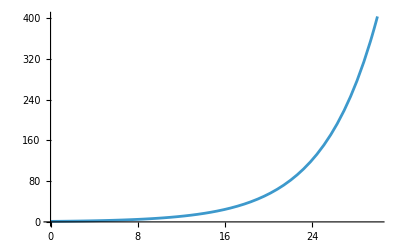

```mathematica
Plot[Exp[t*.2],{t,0,30}]
```

```mathematica
SeriesCoefficient[{CoEq[[1,1]],CoEq[[1,2]],CoEq[[1,3]]}//.{Log[w]->δ},{w,0,-3},{δ,0,0}]
```

{0,0,0}

```mathematica
SeriesCoefficient[{CoEq[[1,1]],CoEq[[1,2]],CoEq[[1,3]]}//.{Log[w]->δ},{w,0,-2},{δ,0,1}]//.solFG//Simplify
```

{-2 (rr1_1[t,rFG]^2 s_0[t,rFG]+f_0[t,rFG] rr1_1[t,rFG] (Τ_1[t,rFG]+2 τ1_1[t,rFG])+RR_1[t,rFG] (rr1_1[t,rFG] s_0[t,rFG]+f_0[t,rFG] τ1_1[t,rFG])-τ1_1[t,rFG] (G[t,rFG]+a_0[t,rFG] (Τ_1[t,rFG]+τ1_1[t,rFG]))),-f_0[t,rFG] rr1_1[t,rFG]+a_0[t,rFG] τ1_1[t,rFG],-rr1_1[t,rFG] s_0[t,rFG]-f_0[t,rFG] τ1_1[t,rFG]}

```mathematica
tmp=SeriesCoefficient[{CoEq[[1,1]],CoEq[[1,2]],CoEq[[1,3]]}//.{Log[w]->δ},{w,0,-2},{δ,0,0}]//.solFG//Simplify
```

{1+G[t,rFG] (Τ_1[t,rFG]+τ1_1[t,rFG])+(Τ_1[t,rFG]+τ1_1[t,rFG]) (G[t,rFG]-f_0[t,rFG] (RR_1[t,rFG]+rr1_1[t,rFG])+a_0[t,rFG] (Τ_1[t,rFG]+τ1_1[t,rFG]))-(RR_1[t,rFG]+rr1_1[t,rFG]) ((RR_1[t,rFG]+rr1_1[t,rFG]) s_0[t,rFG]+f_0[t,rFG] (Τ_1[t,rFG]+τ1_1[t,rFG])),G[t,rFG]-f_0[t,rFG] (RR_1[t,rFG]+rr1_1[t,rFG])+a_0[t,rFG] (Τ_1[t,rFG]+τ1_1[t,rFG]),-((RR_1[t,rFG]+rr1_1[t,rFG]) s_0[t,rFG])-f_0[t,rFG] (Τ_1[t,rFG]+τ1_1[t,rFG])}

```mathematica
soltmp=Solve[0==tmp[[2;;3]],{Subscript[RR, 1][t,rFG],Subscript[Τ, 1][t,rFG]}][[1]]//Simplify
```

{RR_1[t,rFG]→-rr1_1[t,rFG]+(G[t,rFG] f_0[t,rFG])/(f_0[t,rFG]^2+a_0[t,rFG] s_0[t,rFG]),Τ_1[t,rFG]→-(G[t,rFG] s_0[t,rFG])/(f_0[t,rFG]^2+a_0[t,rFG] s_0[t,rFG])-τ1_1[t,rFG]}

```mathematica
tmp//.soltmp//.{rFG->r}//.BCs//Simplify
```

{0,0,0}

```mathematica
soltmp//.{rFG->r}//.BCs//Simplify
```

{RR_1[t,r]→F0[t,r]/(G[t,r] S0[t,r])-rr1_1[t,r],Τ_1[t,r]→-1/G[t,r]-τ1_1[t,r]}

```mathematica
solFG={Subscript[RR, 1]->Function[{t,r},F0[t,r]/(G[t,r] S0[t,r])],Subscript[Τ, 1]->Function[{t,r},-1/G[t,r]],Subscript[τ1, 1]->Function[{t,r},0],Subscript[rr1, 1]->Function[{t,r},0],Subscript[τ1, 2]->Function[{t,r},0],Subscript[rr1, 2]->Function[{t,r},0],Subscript[ρ1, 1]->Function[{t,r},0],Subscript[ρ1, 2]->Function[{t,r},0],Subscript[τ1, 3]->Function[{t,r},0],Subscript[rr1, 3]->Function[{t,r},0],Subscript[Ρ, 1]->Function[{t,r},-(G[t,r] S0[t,r]^2 (S0[t,r] Subscript[a, 1][t,r]+2 F0[t,r] Derivative[0,1][G][t,r])+F0[t,r]^2 (F0[t,r] Derivative[0,1][S0][t,r]+S0[t,r] (-2 Derivative[0,1][F0][t,r]+Derivative[1,0][S0][t,r])))/(2 S0[t,r]^2 (-F0[t,r]^2 G[t,r]+G[t,r]^3 S0[t,r]))],
Subscript[Τ, 2]->Function[{t,r},(F0[t,r] Derivative[0,1][G][t,r]-S0[t,r] Derivative[1,0][G][t,r])/(2 G[t,r]^3 S0[t,r])],Subscript[RR, 2]->Function[{t,r},1/(2 G[t,r]^3 S0[t,r]^3)(-F0[t,r]^2 (S0[t,r] Derivative[0,1][G][t,r]+G[t,r] Derivative[0,1][S0][t,r])+G[t,r] S0[t,r]^2 (G[t,r] Derivative[0,1][G][t,r]-Derivative[1,0][F0][t,r])+F0[t,r] S0[t,r] (S0[t,r] Derivative[1,0][G][t,r]+G[t,r] (Derivative[0,1][F0][t,r]+Derivative[1,0][S0][t,r])))]}
```

{RR_1→Function[{t,r},F0[t,r]/(G[t,r] S0[t,r])],Τ_1→Function[{t,r},-1/G[t,r]],τ1_1→Function[{t,r},0],rr1_1→Function[{t,r},0],τ1_2→Function[{t,r},0],rr1_2→Function[{t,r},0],ρ1_1→Function[{t,r},0],ρ1_2→Function[{t,r},0],τ1_3→Function[{t,r},0],rr1_3→Function[{t,r},0],Ρ_1→Function[{t,r},-(G[t,r] S0[t,r]^2 (S0[t,r] a_1[t,r]+2 F0[t,r] G^(0,1)[t,r])+F0[t,r]^2 (F0[t,r] S0^(0,1)[t,r]+S0[t,r] (-2 F0^(0,1)[t,r]+S0^(1,0)[t,r])))/(2 S0[t,r]^2 (-F0[t,r]^2 G[t,r]+G[t,r]^3 S0[t,r]))],Τ_2→Function[{t,r},(F0[t,r] G^(0,1)[t,r]-S0[t,r] G^(1,0)[t,r])/(2 G[t,r]^3 S0[t,r])],RR_2→Function[{t,r},1/(2 G[t,r]^3 S0[t,r]^3)(-F0[t,r]^2 (S0[t,r] G^(0,1)[t,r]+G[t,r] S0^(0,1)[t,r])+G[t,r] S0[t,r]^2 (G[t,r] G^(0,1)[t,r]-F0^(1,0)[t,r])+F0[t,r] S0[t,r] (S0[t,r] G^(1,0)[t,r]+G[t,r] (F0^(0,1)[t,r]+S0^(1,0)[t,r])))]}

```mathematica
SeriesCoefficient[{CoEq[[1,1]],CoEq[[1,2]],CoEq[[1,3]]}//.{Log[w]->δ},{w,0,-1},{δ,0,1}]//.solFG//Simplify
```

{0,0,0}

```mathematica
SeriesCoefficient[{CoEq[[1,1]],CoEq[[1,2]],CoEq[[1,3]]}//.{Log[w]->δ},{w,0,0},{δ,0,1}]//.solFG//Simplify
```

{0,0,0}

```mathematica
tmp2=SeriesCoefficient[{CoEq[[1,1]],CoEq[[1,2]],CoEq[[1,3]]}//.{Log[w]->δ},{w,0,-1},{δ,0,0}]//.solFG//.{rFG->r}//.BCs//.solEF//Simplify
```

{0,0,0}

```mathematica
soltmp2=Solve[0==tmp2,{Subscript[Ρ, 1][t,r],Subscript[Τ, 2][t,r],Subscript[RR, 2][t,r]}][[1]]//Simplify
```

{Ρ_1[t,r]→-(G[t,r] S0[t,r]^2 (S0[t,r] a_1[t,r]+2 F0[t,r] G^(0,1)[t,r])+F0[t,r]^2 (F0[t,r] S0^(0,1)[t,r]+S0[t,r] (-2 F0^(0,1)[t,r]+S0^(1,0)[t,r])))/(2 S0[t,r]^2 (-F0[t,r]^2 G[t,r]+G[t,r]^3 S0[t,r])),Τ_2[t,r]→(F0[t,r] G^(0,1)[t,r]-S0[t,r] G^(1,0)[t,r])/(2 G[t,r]^3 S0[t,r]),RR_2[t,r]→1/(2 G[t,r]^3 S0[t,r]^3)(-F0[t,r]^2 (S0[t,r] G^(0,1)[t,r]+G[t,r] S0^(0,1)[t,r])+G[t,r] S0[t,r]^2 (G[t,r] G^(0,1)[t,r]-F0^(1,0)[t,r])+F0[t,r] S0[t,r] (S0[t,r] G^(1,0)[t,r]+G[t,r] (F0^(0,1)[t,r]+S0^(1,0)[t,r])))}

```mathematica
tmp2//.solFG//Simplify
```

{0,0,0}

```mathematica
order=3;
```

```mathematica
Clear[A]
```

```mathematica
A[h_,t_,r_]:=h^2 Subscript[a, 0][t,r]+h Subscript[a, 1][t,r]+Subscript[a, 2][t,r]+1/h Subscript[a, 3][t,r];
Σ[h_,t_,r_]:=h^2 Subscript[s, 0][t,r]+h Subscript[s, 1][t,r]+Subscript[s, 2][t,r]+1/h Subscript[s, 3][t,r];
F[h_,t_,r_]:=h^2 Subscript[f, 0][t,r]+h Subscript[f, 1][t,r]+Subscript[f, 2][t,r]+1/h Subscript[f, 3][t,r];
HEF[w_,t_,r_]:=HEFSer[w,t,r,order]//.solFG//Evaluate;
TEF[w_,t_,r_]:=TEFSer[w,t,r,order]//.solFG//Evaluate;
REF[w_,t_,r_]:=REFSer[w,t,r,order]//.solFG//Evaluate;
```

```mathematica
CoEq=FGmetric-Transpose[ΛMat].EFmetric.ΛMat;
```

```mathematica
tmp3=SeriesCoefficient[{CoEq[[1,1]],CoEq[[1,2]],CoEq[[1,3]]}//.{Log[w]->δ},{w,0,0},{δ,0,0}]//.solFG//.BCs;
```

```mathematica
tmp3=Simplify[tmp3];
```

```mathematica
soltmp3=Solve[0==tmp3[[1;;3]],{Subscript[Ρ, 2][t,rFG],Subscript[Τ, 3][t,rFG],Subscript[RR, 3][t,rFG]}][[1]]//Simplify;
```

```mathematica
tmp3//.soltmp3//Simplify
```

{0,0,0}

```mathematica
solFG=Join[solFG,{Subscript[Ρ, 2]->Function[{t,rFG},Evaluate[Subscript[Ρ, 2][t,rFG]/.soltmp3]],Subscript[Τ, 3]->Function[{t,rFG},Evaluate[Subscript[Τ, 3][t,rFG]/.soltmp3]],Subscript[RR, 3]->Function[{t,rFG},Evaluate[Subscript[RR, 3][t,rFG]/.soltmp3]]}];
```

```mathematica
Collect[HEF[w,t,r]//.solFG//.solEF,w,Simplify]
```

1/w+w^2 (Ρ_3[t,r]+Log[w] ρ1_3[t,r])-(G[t,r] S0[t,r]^2 (S0[t,r] a_1[t,r]+2 F0[t,r] G^(0,1)[t,r])+F0[t,r]^2 (F0[t,r] S0^(0,1)[t,r]+S0[t,r] (-2 F0^(0,1)[t,r]+S0^(1,0)[t,r])))/(2 S0[t,r]^2 (-F0[t,r]^2 G[t,r]+G[t,r]^3 S0[t,r]))-1/(48 G[t,r]^3 S0[t,r]^4)w ((G[t,r] S0[t,r]^2 (5 F0[t,r]^2 (B0^(0,1)[t,r])^2-10 F0[t,r] S0[t,r] B0^(0,1)[t,r] B0^(1,0)[t,r]+S0[t,r] (G[t,r]^2 (B0^(0,1)[t,r])^2+5 S0[t,r] (B0^(1,0)[t,r])^2)))/B0[t,r]^2+1/B0[t,r]2 S0[t,r] (4 G[t,r]^2 S0[t,r]^2 B0^(0,1)[t,r] G^(0,1)[t,r]+G[t,r]^3 S0[t,r] (2 S0[t,r]^2+B0^(0,1)[t,r] S0^(0,1)[t,r]-2 S0[t,r] B0^(0,2)[t,r])+4 S0[t,r] (-F0[t,r] B0^(0,1)[t,r]+S0[t,r] B0^(1,0)[t,r]) (-F0[t,r] G^(0,1)[t,r]+S0[t,r] G^(1,0)[t,r])+G[t,r] (F0[t,r]^2 (3 B0^(0,1)[t,r] S0^(0,1)[t,r]-4 S0[t,r] B0^(0,2)[t,r])+F0[t,r] S0[t,r] (S0^(0,1)[t,r] B0^(1,0)[t,r]-B0^(0,1)[t,r] (2 F0^(0,1)[t,r]+5 S0^(1,0)[t,r])+8 S0[t,r] B0^(1,1)[t,r])+S0[t,r]^2 (-2 F0^(0,1)[t,r] B0^(1,0)[t,r]+4 B0^(0,1)[t,r] F0^(1,0)[t,r]+B0^(1,0)[t,r] S0^(1,0)[t,r]-4 S0[t,r] B0^(2,0)[t,r])))-1/((F0[t,r]^2-G[t,r]^2 S0[t,r])^2)2 (F0[t,r]^6 (-19 G[t,r] (S0^(0,1)[t,r])^2-10 S0[t,r] (G^(0,1)[t,r] S0^(0,1)[t,r]-G[t,r] S0^(0,2)[t,r]))+2 F0[t,r]^5 S0[t,r] (G[t,r] S0^(0,1)[t,r] (13 F0^(0,1)[t,r]+6 S0^(1,0)[t,r])+5 S0[t,r] (2 F0^(0,1)[t,r] G^(0,1)[t,r]-2 G[t,r] F0^(0,2)[t,r]+S0^(0,1)[t,r] G^(1,0)[t,r]-G^(0,1)[t,r] S0^(1,0)[t,r]))+2 F0[t,r] G[t,r]^2 S0[t,r]^3 (G[t,r]^3 (-5 F0^(0,1)[t,r] S0^(0,1)[t,r]+2 S0[t,r] F0^(0,2)[t,r])+12 S0[t,r]^2 a_1[t,r] F0^(1,0)[t,r]+12 G[t,r] S0[t,r] (S0[t,r] G^(0,1)[t,r] (a_1[t,r]-2 G^(1,0)[t,r])+F0^(1,0)[t,r] (-2 F0^(0,1)[t,r]+S0^(1,0)[t,r]))-G[t,r]^2 S0[t,r] (14 F0^(0,1)[t,r] G^(0,1)[t,r]+S0^(0,1)[t,r] G^(1,0)[t,r]+11 G^(0,1)[t,r] S0^(1,0)[t,r]+6 S0[t,r] (a_1^(0,1)[t,r]-2 G^(1,1)[t,r])))+4 F0[t,r]^3 G[t,r]^2 S0[t,r]^2 (-G[t,r] S0^(0,1)[t,r] (16 F0^(0,1)[t,r]+3 S0^(1,0)[t,r])+S0[t,r] (-22 F0^(0,1)[t,r] G^(0,1)[t,r]+3 a_1[t,r] S0^(0,1)[t,r]+4 G[t,r] F0^(0,2)[t,r]-8 S0^(0,1)[t,r] G^(1,0)[t,r]+8 G^(0,1)[t,r] S0^(1,0)[t,r])+3 S0[t,r]^2 (a_1^(0,1)[t,r]-2 G^(1,1)[t,r]))+F0[t,r]^4 S0[t,r] (2 G[t,r]^2 S0[t,r] (17 G^(0,1)[t,r] S0^(0,1)[t,r]+10 S0[t,r] G^(0,2)[t,r])+G[t,r]^3 (26 (S0^(0,1)[t,r])^2-8 S0[t,r] S0^(0,2)[t,r])+10 S0[t,r]^2 G^(1,0)[t,r] (-2 F0^(0,1)[t,r]+S0^(1,0)[t,r])+G[t,r] S0[t,r] (4 (F0^(0,1)[t,r])^2-10 S0^(0,1)[t,r] F0^(1,0)[t,r]-24 F0^(0,1)[t,r] S0^(1,0)[t,r]+11 (S0^(1,0)[t,r])^2+20 S0[t,r] F0^(1,1)[t,r]-10 S0[t,r] S0^(2,0)[t,r]))+G[t,r]^3 S0[t,r]^4 (2 G[t,r]^3 (G^(0,1)[t,r] S0^(0,1)[t,r]-2 S0[t,r] G^(0,2)[t,r])-24 S0[t,r]^2 a_1[t,r] G^(1,0)[t,r]+2 G[t,r] S0[t,r] (12 G^(0,1)[t,r] F0^(1,0)[t,r]+2 F0^(0,1)[t,r] G^(1,0)[t,r]-G^(1,0)[t,r] S0^(1,0)[t,r]+6 S0[t,r] a_1^(1,0)[t,r])+G[t,r]^2 (4 (F0^(0,1)[t,r])^2+2 S0^(0,1)[t,r] F0^(1,0)[t,r]-(S0^(1,0)[t,r])^2-4 S0[t,r] F0^(1,1)[t,r]+2 S0[t,r] S0^(2,0)[t,r]))+F0[t,r]^2 G[t,r]^2 S0[t,r]^2 (5 G[t,r]^3 (S0^(0,1)[t,r])^2+2 G[t,r] S0[t,r] (20 (F0^(0,1)[t,r])^2+11 G[t,r] G^(0,1)[t,r] S0^(0,1)[t,r]-G[t,r]^2 S0^(0,2)[t,r]+16 S0^(0,1)[t,r] F0^(1,0)[t,r]+12 F0^(0,1)[t,r] S0^(1,0)[t,r]-11 (S0^(1,0)[t,r])^2)-12 S0[t,r]^3 a_1^(1,0)[t,r]-4 S0[t,r]^2 (4 G[t,r]^2 G^(0,2)[t,r]-6 G^(0,1)[t,r] F0^(1,0)[t,r]-16 F0^(0,1)[t,r] G^(1,0)[t,r]+8 G^(1,0)[t,r] S0^(1,0)[t,r]+3 a_1[t,r] (2 F0^(0,1)[t,r]+S0^(1,0)[t,r])-2 G[t,r] (6 (G^(0,1)[t,r])^2-2 F0^(1,1)[t,r]+S0^(2,0)[t,r])))))

```mathematica
Collect[REF[w,t,r]//.solFG//.solEF,w,Simplify]
```

r+(w F0[t,r])/(G[t,r] S0[t,r])+1/(2 G[t,r]^3 S0[t,r]^3)w^2 (-F0[t,r]^2 (S0[t,r] G^(0,1)[t,r]+G[t,r] S0^(0,1)[t,r])+G[t,r] S0[t,r]^2 (G[t,r] G^(0,1)[t,r]-F0^(1,0)[t,r])+F0[t,r] S0[t,r] (S0[t,r] G^(1,0)[t,r]+G[t,r] (F0^(0,1)[t,r]+S0^(1,0)[t,r])))+1/(144 B0[t,r]^2 G[t,r]^5 S0[t,r]^5)w^3 (G[t,r]^2 S0[t,r]^2 (-5 F0[t,r]^3 (B0^(0,1)[t,r])^2+10 F0[t,r]^2 S0[t,r] B0^(0,1)[t,r] B0^(1,0)[t,r]-12 G[t,r]^2 S0[t,r]^2 B0^(0,1)[t,r] B0^(1,0)[t,r]+F0[t,r] S0[t,r] (11 G[t,r]^2 (B0^(0,1)[t,r])^2-5 S0[t,r] (B0^(1,0)[t,r])^2))-2 B0[t,r] G[t,r] S0[t,r] (F0[t,r]^3 (3 G[t,r] B0^(0,1)[t,r] S0^(0,1)[t,r]+4 S0[t,r] (B0^(0,1)[t,r] G^(0,1)[t,r]-G[t,r] B0^(0,2)[t,r]))+6 G[t,r]^2 S0[t,r]^2 (G[t,r] B0^(0,1)[t,r] S0^(1,0)[t,r]+2 S0[t,r] (G^(0,1)[t,r] B0^(1,0)[t,r]-G[t,r] B0^(1,1)[t,r]))+F0[t,r]^2 S0[t,r] (-4 S0[t,r] (G^(0,1)[t,r] B0^(1,0)[t,r]+B0^(0,1)[t,r] G^(1,0)[t,r])+G[t,r] (S0^(0,1)[t,r] B0^(1,0)[t,r]-B0^(0,1)[t,r] (2 F0^(0,1)[t,r]+5 S0^(1,0)[t,r])+8 S0[t,r] B0^(1,1)[t,r]))+F0[t,r] S0[t,r] (-8 G[t,r]^2 S0[t,r] B0^(0,1)[t,r] G^(0,1)[t,r]+G[t,r]^3 (2 S0[t,r]^2-5 B0^(0,1)[t,r] S0^(0,1)[t,r]+10 S0[t,r] B0^(0,2)[t,r])+4 S0[t,r]^2 B0^(1,0)[t,r] G^(1,0)[t,r]+G[t,r] S0[t,r] (-2 F0^(0,1)[t,r] B0^(1,0)[t,r]+4 B0^(0,1)[t,r] F0^(1,0)[t,r]+B0^(1,0)[t,r] S0^(1,0)[t,r]-4 S0[t,r] B0^(2,0)[t,r])))-2 B0[t,r]^2 (F0[t,r]^3 (-41 G[t,r]^2 (S0^(0,1)[t,r])^2+12 S0[t,r]^2 (-3 (G^(0,1)[t,r])^2+G[t,r] G^(0,2)[t,r])+2 G[t,r] S0[t,r] (-25 G^(0,1)[t,r] S0^(0,1)[t,r]+7 G[t,r] S0^(0,2)[t,r]))+2 F0[t,r]^2 S0[t,r] (36 S0[t,r]^2 G^(0,1)[t,r] G^(1,0)[t,r]+G[t,r] S0[t,r] (26 F0^(0,1)[t,r] G^(0,1)[t,r]+19 S0^(0,1)[t,r] G^(1,0)[t,r]+23 G^(0,1)[t,r] S0^(1,0)[t,r]-12 S0[t,r] G^(1,1)[t,r])+G[t,r]^2 (29 F0^(0,1)[t,r] S0^(0,1)[t,r]+30 S0^(0,1)[t,r] S0^(1,0)[t,r]-4 S0[t,r] (2 F0^(0,2)[t,r]+3 S0^(1,1)[t,r])))+12 G[t,r] S0[t,r]^3 (3 S0[t,r] F0^(1,0)[t,r] G^(1,0)[t,r]-G[t,r]^2 (3 F0^(0,1)[t,r] G^(0,1)[t,r]+G^(0,1)[t,r] S0^(1,0)[t,r]-2 S0[t,r] G^(1,1)[t,r])+G[t,r] (F0^(0,1)[t,r] F0^(1,0)[t,r]+2 F0^(1,0)[t,r] S0^(1,0)[t,r]-S0[t,r] (2 G^(0,1)[t,r] G^(1,0)[t,r]+F0^(2,0)[t,r])))-F0[t,r] S0[t,r]^2 (G[t,r]^3 (-46 G^(0,1)[t,r] S0^(0,1)[t,r]+20 S0[t,r] G^(0,2)[t,r])+36 S0[t,r]^2 (G^(1,0)[t,r])^2+2 G[t,r] S0[t,r] (24 G^(0,1)[t,r] F0^(1,0)[t,r]+20 F0^(0,1)[t,r] G^(1,0)[t,r]+17 G^(1,0)[t,r] S0^(1,0)[t,r]-6 S0[t,r] G^(2,0)[t,r])+G[t,r]^2 (16 (F0^(0,1)[t,r])^2+38 S0^(0,1)[t,r] F0^(1,0)[t,r]+36 F0^(0,1)[t,r] S0^(1,0)[t,r]+23 (S0^(1,0)[t,r])^2-2 S0[t,r] (18 (G^(0,1)[t,r])^2+14 F0^(1,1)[t,r]+5 S0^(2,0)[t,r])))))

```mathematica
Collect[TEF[w,t,r]//.solFG//.solEF,w,Simplify]
```

t-w/G[t,r]+(w^2 (F0[t,r] G^(0,1)[t,r]-S0[t,r] G^(1,0)[t,r]))/(2 G[t,r]^3 S0[t,r])+1/(144 B0[t,r]^2 G[t,r]^5 S0[t,r]^4)w^3 (G[t,r]^2 S0[t,r]^2 (5 F0[t,r]^2 (B0^(0,1)[t,r])^2-10 F0[t,r] S0[t,r] B0^(0,1)[t,r] B0^(1,0)[t,r]+S0[t,r] (G[t,r]^2 (B0^(0,1)[t,r])^2+5 S0[t,r] (B0^(1,0)[t,r])^2))+2 B0[t,r] G[t,r] S0[t,r] (4 G[t,r]^2 S0[t,r]^2 B0^(0,1)[t,r] G^(0,1)[t,r]+G[t,r]^3 S0[t,r] (2 S0[t,r]^2+B0^(0,1)[t,r] S0^(0,1)[t,r]-2 S0[t,r] B0^(0,2)[t,r])+4 S0[t,r] (-F0[t,r] B0^(0,1)[t,r]+S0[t,r] B0^(1,0)[t,r]) (-F0[t,r] G^(0,1)[t,r]+S0[t,r] G^(1,0)[t,r])+G[t,r] (F0[t,r]^2 (3 B0^(0,1)[t,r] S0^(0,1)[t,r]-4 S0[t,r] B0^(0,2)[t,r])+F0[t,r] S0[t,r] (S0^(0,1)[t,r] B0^(1,0)[t,r]-B0^(0,1)[t,r] (2 F0^(0,1)[t,r]+5 S0^(1,0)[t,r])+8 S0[t,r] B0^(1,1)[t,r])+S0[t,r]^2 (-2 F0^(0,1)[t,r] B0^(1,0)[t,r]+4 B0^(0,1)[t,r] F0^(1,0)[t,r]+B0^(1,0)[t,r] S0^(1,0)[t,r]-4 S0[t,r] B0^(2,0)[t,r])))+2 B0[t,r]^2 (2 G[t,r]^3 S0[t,r]^2 (-G^(0,1)[t,r] S0^(0,1)[t,r]+2 S0[t,r] G^(0,2)[t,r])-36 S0[t,r]^2 (F0[t,r] G^(0,1)[t,r]-S0[t,r] G^(1,0)[t,r])^2+2 G[t,r] S0[t,r] (F0[t,r]^2 (-7 G^(0,1)[t,r] S0^(0,1)[t,r]+6 S0[t,r] G^(0,2)[t,r])+F0[t,r] S0[t,r] (8 F0^(0,1)[t,r] G^(0,1)[t,r]+S0^(0,1)[t,r] G^(1,0)[t,r]+5 G^(0,1)[t,r] S0^(1,0)[t,r]-12 S0[t,r] G^(1,1)[t,r])+S0[t,r]^2 (-6 G^(0,1)[t,r] F0^(1,0)[t,r]-2 F0^(0,1)[t,r] G^(1,0)[t,r]+G^(1,0)[t,r] S0^(1,0)[t,r]+6 S0[t,r] G^(2,0)[t,r]))+G[t,r]^2 (-5 F0[t,r]^2 (S0^(0,1)[t,r])^2+2 F0[t,r] S0[t,r] (5 F0^(0,1)[t,r] S0^(0,1)[t,r]+F0[t,r] S0^(0,2)[t,r])+S0[t,r]^2 (-4 (F0^(0,1)[t,r])^2-4 F0[t,r] F0^(0,2)[t,r]-2 S0^(0,1)[t,r] F0^(1,0)[t,r]+(S0^(1,0)[t,r])^2)+2 S0[t,r]^3 (6 (G^(0,1)[t,r])^2+2 F0^(1,1)[t,r]-S0^(2,0)[t,r]))))

```mathematica
Series[G11[w,t,rFG]/.Solve[0==CoEq[[2,2]],G11[w,t,rFG]],{w,0,0}]//.Join[BCs,solFG,solEF]//Simplify
```

{(-G[t,rFG]^2+F0[t,rFG]^2/S0[t,rFG])/w^2-1/(24 (B0[t,rFG]^2 G[t,rFG]^3 S0[t,rFG]^5))(G[t,rFG] S0[t,rFG]^2 (F0[t,rFG]^4 (B0^(0,1)[t,rFG])^2-2 F0[t,rFG]^3 S0[t,rFG] B0^(0,1)[t,rFG] B0^(1,0)[t,rFG]+2 F0[t,rFG] G[t,rFG]^2 S0[t,rFG]^2 B0^(0,1)[t,rFG] B0^(1,0)[t,rFG]+F0[t,rFG]^2 S0[t,rFG] (-2 G[t,rFG]^2 (B0^(0,1)[t,rFG])^2+S0[t,rFG] (B0^(1,0)[t,rFG])^2)+G[t,rFG]^2 S0[t,rFG]^2 (G[t,rFG]^2 (B0^(0,1)[t,rFG])^2+5 S0[t,rFG] (B0^(1,0)[t,rFG])^2))+2 B0[t,rFG] S0[t,rFG]^2 (2 F0[t,rFG]^4 (B0^(0,1)[t,rFG] G^(0,1)[t,rFG]-G[t,rFG] B0^(0,2)[t,rFG])+F0[t,rFG] G[t,rFG]^2 S0[t,rFG] (4 S0[t,rFG] (2 G^(0,1)[t,rFG] B0^(1,0)[t,rFG]-B0^(0,1)[t,rFG] G^(1,0)[t,rFG])+G[t,rFG] (S0^(0,1)[t,rFG] B0^(1,0)[t,rFG]+B0^(0,1)[t,rFG] (-2 F0^(0,1)[t,rFG]+S0^(1,0)[t,rFG])-4 S0[t,rFG] B0^(1,1)[t,rFG]))+2 F0[t,rFG]^3 (-S0[t,rFG] (G^(0,1)[t,rFG] B0^(1,0)[t,rFG]+B0^(0,1)[t,rFG] G^(1,0)[t,rFG])+G[t,rFG] (S0^(0,1)[t,rFG] B0^(1,0)[t,rFG]+B0^(0,1)[t,rFG] (F0^(0,1)[t,rFG]-2 S0^(1,0)[t,rFG])+2 S0[t,rFG] B0^(1,1)[t,rFG]))+G[t,rFG]^2 S0[t,rFG] (4 G[t,rFG]^2 S0[t,rFG] B0^(0,1)[t,rFG] G^(0,1)[t,rFG]+G[t,rFG]^3 (2 S0[t,rFG]^2+B0^(0,1)[t,rFG] S0^(0,1)[t,rFG]-2 S0[t,rFG] B0^(0,2)[t,rFG])+4 S0[t,rFG]^2 B0^(1,0)[t,rFG] G^(1,0)[t,rFG]+G[t,rFG] S0[t,rFG] (-2 F0^(0,1)[t,rFG] B0^(1,0)[t,rFG]+4 B0^(0,1)[t,rFG] F0^(1,0)[t,rFG]+B0^(1,0)[t,rFG] S0^(1,0)[t,rFG]-4 S0[t,rFG] B0^(2,0)[t,rFG]))-F0[t,rFG]^2 (6 G[t,rFG]^2 S0[t,rFG] B0^(0,1)[t,rFG] G^(0,1)[t,rFG]+G[t,rFG]^3 (2 S0[t,rFG]^2+B0^(0,1)[t,rFG] S0^(0,1)[t,rFG]-4 S0[t,rFG] B0^(0,2)[t,rFG])-2 S0[t,rFG]^2 B0^(1,0)[t,rFG] G^(1,0)[t,rFG]+2 G[t,rFG] S0[t,rFG] (2 F0^(0,1)[t,rFG] B0^(1,0)[t,rFG]-B0^(0,1)[t,rFG] F0^(1,0)[t,rFG]-B0^(1,0)[t,rFG] S0^(1,0)[t,rFG]+S0[t,rFG] B0^(2,0)[t,rFG])))-2 B0[t,rFG]^2 (F0[t,rFG]^2-G[t,rFG]^2 S0[t,rFG]) (2 G[t,rFG]^2 S0[t,rFG]^2 (-G^(0,1)[t,rFG] S0^(0,1)[t,rFG]+2 S0[t,rFG] G^(0,2)[t,rFG])-2 S0[t,rFG] (F0[t,rFG] G^(0,1)[t,rFG]-S0[t,rFG] G^(1,0)[t,rFG]) (F0[t,rFG] S0^(0,1)[t,rFG]+S0[t,rFG] (-2 F0^(0,1)[t,rFG]+S0^(1,0)[t,rFG]))+G[t,rFG] (-5 F0[t,rFG]^2 (S0^(0,1)[t,rFG])^2+2 F0[t,rFG] S0[t,rFG] (5 F0^(0,1)[t,rFG] S0^(0,1)[t,rFG]+F0[t,rFG] S0^(0,2)[t,rFG])+S0[t,rFG]^2 (-4 (F0^(0,1)[t,rFG])^2-4 F0[t,rFG] F0^(0,2)[t,rFG]-2 S0^(0,1)[t,rFG] F0^(1,0)[t,rFG]+(S0^(1,0)[t,rFG])^2)+S0[t,rFG]^3 (4 F0^(1,1)[t,rFG]-2 S0^(2,0)[t,rFG]))))+O[w]^1}

```mathematica
Series[G12[w,t,rFG]/.Solve[0==CoEq[[2,3]],G12[w,t,rFG]],{w,0,0}]//.Join[BCs,solFG,solEF]//Simplify
```

{F0[t,rFG]/w^2+1/(24 B0[t,rFG]^2 G[t,rFG]^3 S0[t,rFG]^4)(-G[t,rFG] S0[t,rFG]^2 (F0[t,rFG]^3 (B0^(0,1)[t,rFG])^2-2 F0[t,rFG]^2 S0[t,rFG] B0^(0,1)[t,rFG] B0^(1,0)[t,rFG]+6 G[t,rFG]^2 S0[t,rFG]^2 B0^(0,1)[t,rFG] B0^(1,0)[t,rFG]+F0[t,rFG] S0[t,rFG] (-G[t,rFG]^2 (B0^(0,1)[t,rFG])^2+S0[t,rFG] (B0^(1,0)[t,rFG])^2))+2 B0[t,rFG] S0[t,rFG]^2 (F0[t,rFG]^3 (-2 B0^(0,1)[t,rFG] G^(0,1)[t,rFG]+2 G[t,rFG] B0^(0,2)[t,rFG])+3 G[t,rFG]^2 S0[t,rFG] (-G[t,rFG] B0^(0,1)[t,rFG] S0^(1,0)[t,rFG]+S0[t,rFG] (-2 G^(0,1)[t,rFG] B0^(1,0)[t,rFG]+2 G[t,rFG] B0^(1,1)[t,rFG]))-2 F0[t,rFG]^2 (-S0[t,rFG] (G^(0,1)[t,rFG] B0^(1,0)[t,rFG]+B0^(0,1)[t,rFG] G^(1,0)[t,rFG])+G[t,rFG] (S0^(0,1)[t,rFG] B0^(1,0)[t,rFG]+B0^(0,1)[t,rFG] (F0^(0,1)[t,rFG]-2 S0^(1,0)[t,rFG])+2 S0[t,rFG] B0^(1,1)[t,rFG]))+F0[t,rFG] (4 G[t,rFG]^2 S0[t,rFG] B0^(0,1)[t,rFG] G^(0,1)[t,rFG]+G[t,rFG]^3 (2 S0[t,rFG]^2+B0^(0,1)[t,rFG] S0^(0,1)[t,rFG]-2 S0[t,rFG] B0^(0,2)[t,rFG])-2 S0[t,rFG]^2 B0^(1,0)[t,rFG] G^(1,0)[t,rFG]+2 G[t,rFG] S0[t,rFG] (2 F0^(0,1)[t,rFG] B0^(1,0)[t,rFG]-B0^(0,1)[t,rFG] F0^(1,0)[t,rFG]-B0^(1,0)[t,rFG] S0^(1,0)[t,rFG]+S0[t,rFG] B0^(2,0)[t,rFG])))+2 B0[t,rFG]^2 F0[t,rFG] (2 G[t,rFG]^2 S0[t,rFG]^2 (-G^(0,1)[t,rFG] S0^(0,1)[t,rFG]+2 S0[t,rFG] G^(0,2)[t,rFG])-2 S0[t,rFG] (F0[t,rFG] G^(0,1)[t,rFG]-S0[t,rFG] G^(1,0)[t,rFG]) (F0[t,rFG] S0^(0,1)[t,rFG]+S0[t,rFG] (-2 F0^(0,1)[t,rFG]+S0^(1,0)[t,rFG]))+G[t,rFG] (-5 F0[t,rFG]^2 (S0^(0,1)[t,rFG])^2+2 F0[t,rFG] S0[t,rFG] (5 F0^(0,1)[t,rFG] S0^(0,1)[t,rFG]+F0[t,rFG] S0^(0,2)[t,rFG])+S0[t,rFG]^2 (-4 (F0^(0,1)[t,rFG])^2-4 F0[t,rFG] F0^(0,2)[t,rFG]-2 S0^(0,1)[t,rFG] F0^(1,0)[t,rFG]+(S0^(1,0)[t,rFG])^2)+S0[t,rFG]^3 (4 F0^(1,1)[t,rFG]-2 S0^(2,0)[t,rFG]))))+O[w]^1}

```mathematica
Series[G22[w,t,rFG]/.Solve[0==CoEq[[3,3]],G22[w,t,rFG]],{w,0,0}]//.Join[BCs,solFG,solEF]//Simplify
```

{S0[t,rFG]/w^2+1/(24 B0[t,rFG]^2 G[t,rFG]^3 S0[t,rFG]^3)(-G[t,rFG] S0[t,rFG]^2 (F0[t,rFG]^2 (B0^(0,1)[t,rFG])^2-2 F0[t,rFG] S0[t,rFG] B0^(0,1)[t,rFG] B0^(1,0)[t,rFG]+S0[t,rFG] (5 G[t,rFG]^2 (B0^(0,1)[t,rFG])^2+S0[t,rFG] (B0^(1,0)[t,rFG])^2))+4 B0[t,rFG] S0[t,rFG]^2 (-G[t,rFG]^2 S0[t,rFG] B0^(0,1)[t,rFG] G^(0,1)[t,rFG]+G[t,rFG]^3 (S0[t,rFG]^2-B0^(0,1)[t,rFG] S0^(0,1)[t,rFG]+2 S0[t,rFG] B0^(0,2)[t,rFG])-(F0[t,rFG] B0^(0,1)[t,rFG]-S0[t,rFG] B0^(1,0)[t,rFG]) (F0[t,rFG] G^(0,1)[t,rFG]-S0[t,rFG] G^(1,0)[t,rFG])+G[t,rFG] (F0[t,rFG]^2 B0^(0,2)[t,rFG]-F0[t,rFG] (S0^(0,1)[t,rFG] B0^(1,0)[t,rFG]+B0^(0,1)[t,rFG] (F0^(0,1)[t,rFG]-2 S0^(1,0)[t,rFG])+2 S0[t,rFG] B0^(1,1)[t,rFG])+S0[t,rFG] (2 F0^(0,1)[t,rFG] B0^(1,0)[t,rFG]-B0^(0,1)[t,rFG] F0^(1,0)[t,rFG]-B0^(1,0)[t,rFG] S0^(1,0)[t,rFG]+S0[t,rFG] B0^(2,0)[t,rFG])))+2 B0[t,rFG]^2 (2 G[t,rFG]^2 S0[t,rFG]^2 (-G^(0,1)[t,rFG] S0^(0,1)[t,rFG]+2 S0[t,rFG] G^(0,2)[t,rFG])-2 S0[t,rFG] (F0[t,rFG] G^(0,1)[t,rFG]-S0[t,rFG] G^(1,0)[t,rFG]) (F0[t,rFG] S0^(0,1)[t,rFG]+S0[t,rFG] (-2 F0^(0,1)[t,rFG]+S0^(1,0)[t,rFG]))+G[t,rFG] (-5 F0[t,rFG]^2 (S0^(0,1)[t,rFG])^2+2 F0[t,rFG] S0[t,rFG] (5 F0^(0,1)[t,rFG] S0^(0,1)[t,rFG]+F0[t,rFG] S0^(0,2)[t,rFG])+S0[t,rFG]^2 (-4 (F0^(0,1)[t,rFG])^2-4 F0[t,rFG] F0^(0,2)[t,rFG]-2 S0^(0,1)[t,rFG] F0^(1,0)[t,rFG]+(S0^(1,0)[t,rFG])^2)+S0[t,rFG]^3 (4 F0^(1,1)[t,rFG]-2 S0^(2,0)[t,rFG]))))+O[w]^1}

```mathematica
B[h_,t_,r_]:=h^2 Subscript[b, 0][t,r]+h Subscript[b, 1][t,r]+Subscript[b, 2][t,r]+1/h Subscript[b, 3][t,r];
```

```mathematica
Series[B[HEF[w,t,rFG],TEF[w,t,rFG],REF[w,t,rFG]],{w,0,0}]//.Join[BCs,solFG,solEF]//Simplify
```

B0[t,rFG]/w^2+1/(24 B0[t,rFG] G[t,rFG]^3 S0[t,rFG]^4)(G[t,rFG] S0[t,rFG]^2 (-F0[t,rFG]^2 (B0^(0,1)[t,rFG])^2+2 F0[t,rFG] S0[t,rFG] B0^(0,1)[t,rFG] B0^(1,0)[t,rFG]+S0[t,rFG] (G[t,rFG]^2 (B0^(0,1)[t,rFG])^2-S0[t,rFG] (B0^(1,0)[t,rFG])^2))-B0[t,rFG] S0[t,rFG] (-2 G[t,rFG]^2 S0[t,rFG]^2 B0^(0,1)[t,rFG] G^(0,1)[t,rFG]+G[t,rFG]^3 S0[t,rFG] (8 S0[t,rFG]^2+B0^(0,1)[t,rFG] S0^(0,1)[t,rFG]-2 S0[t,rFG] B0^(0,2)[t,rFG])-2 S0[t,rFG] (-F0[t,rFG] B0^(0,1)[t,rFG]+S0[t,rFG] B0^(1,0)[t,rFG]) (-F0[t,rFG] G^(0,1)[t,rFG]+S0[t,rFG] G^(1,0)[t,rFG])+G[t,rFG] (F0[t,rFG]^2 (-3 B0^(0,1)[t,rFG] S0^(0,1)[t,rFG]+2 S0[t,rFG] B0^(0,2)[t,rFG])+F0[t,rFG] S0[t,rFG] (S0^(0,1)[t,rFG] B0^(1,0)[t,rFG]+B0^(0,1)[t,rFG] (4 F0^(0,1)[t,rFG]+S0^(1,0)[t,rFG])-4 S0[t,rFG] B0^(1,1)[t,rFG])+S0[t,rFG]^2 (-2 F0^(0,1)[t,rFG] B0^(1,0)[t,rFG]-2 B0^(0,1)[t,rFG] F0^(1,0)[t,rFG]+B0^(1,0)[t,rFG] S0^(1,0)[t,rFG]+2 S0[t,rFG] B0^(2,0)[t,rFG])))+B0[t,rFG]^2 (2 G[t,rFG]^2 S0[t,rFG]^2 (G^(0,1)[t,rFG] S0^(0,1)[t,rFG]-2 S0[t,rFG] G^(0,2)[t,rFG])+2 S0[t,rFG] (F0[t,rFG] G^(0,1)[t,rFG]-S0[t,rFG] G^(1,0)[t,rFG]) (F0[t,rFG] S0^(0,1)[t,rFG]+S0[t,rFG] (-2 F0^(0,1)[t,rFG]+S0^(1,0)[t,rFG]))+G[t,rFG] (5 F0[t,rFG]^2 (S0^(0,1)[t,rFG])^2-2 F0[t,rFG] S0[t,rFG] (5 F0^(0,1)[t,rFG] S0^(0,1)[t,rFG]+F0[t,rFG] S0^(0,2)[t,rFG])+S0[t,rFG]^2 (4 (F0^(0,1)[t,rFG])^2+4 F0[t,rFG] F0^(0,2)[t,rFG]+2 S0^(0,1)[t,rFG] F0^(1,0)[t,rFG]-(S0^(1,0)[t,rFG])^2)+S0[t,rFG]^3 (-4 F0^(1,1)[t,rFG]+2 S0^(2,0)[t,rFG]))))+O[w]^1

### Boundary metric

```mathematica
coBd = {t,rFG,θ,ϕ};
NdimBd = Length[coBd];
```

```mathematica
gBd=({{-G[t,rFG]^2+F0[t,rFG]^2/S0[t,rFG], F0[t,rFG], 0, 0}, {F0[t,rFG], S0[t,rFG], 0, 0}, {0, 0, B0[t,rFG], 0}, {0, 0, 0, B0[t,rFG] Sin[θ]^2}});
gupBd=Inverse[gBd]//Simplify;
```

### Christoffel Symbols

```mathematica
ChrBd=Table[
Simplify[(1/2)*Sum[gupBd[[μ,α]]*(
D[gBd[[ν,α]],coBd[[ρ]]]+D[gBd[[ρ,α]],coBd[[ν]]]-D[gBd[[ν,ρ]],coBd[[α]]]),
{α,1,NdimBd}]],
{μ,1,NdimBd},{ν,1,NdimBd},{ρ,1,NdimBd}];
```

### Riemann tensor

```mathematica
Clear[λ]
```

```mathematica
RdownfunBd[μ_,ν_,ρ_,σ_]:=Simplify[Sum[gBd[[μ,λ]](D[ChrBd[[λ,σ,ν]],coBd[[ρ]]] - D[ChrBd[[λ,ρ,ν]],coBd[[σ]]] + Sum[ChrBd[[λ,ρ,α]]*ChrBd[[α,σ,ν]],{α,1,NdimBd}]-Sum[ChrBd[[λ,σ,α]]*ChrBd[[α,ρ,ν]],{α,1,NdimBd}]),{λ,1,NdimBd}]];
```

```mathematica
RdownBd=Table[RdownfunBd[μ,ν,ρ,σ],{μ,1,NdimBd},{ν,1,NdimBd},{ρ,1,NdimBd},{σ,1,NdimBd}];
```

```mathematica
RiemannBd=Table[Sum[gupBd[[μ,λ]]RdownBd[[λ,ν,ρ,σ]],{λ,1,NdimBd}],{μ,1,NdimBd},{ν,1,NdimBd},{ρ,1,NdimBd},{σ,1,NdimBd}];
```

### Ricci and Einstein tensors

```mathematica
RicciBd=Table[Simplify[Sum[RiemannBd[[λ,μ,λ,ν]],{λ,1,NdimBd}]],{μ,1,NdimBd},{ν,1,NdimBd}];
RBd=Sum[gupBd[[μ,ν]]RicciBd[[μ,ν]],{μ,1,NdimBd},{ν,1,NdimBd}]//Simplify;
```

### Ricci and Einstein tensors

```mathematica
explicitG2=Simplify[-1/2(RicciBd-1/6 RBd gBd)];
```

```mathematica
[[1,3,3]]-explicitG2[[1,1]]
```

0

```mathematica
[[1,3,3]]-explicitG2[[1,2]]
```

0

```mathematica
%222[[1,3,3]]-explicitG2[[2,2]]
```

0

```mathematica
%227[[3,3]]-explicitG2[[3,3]]
```

0

```mathematica
explicitG2
```

{{-1/(24 B0[t,rFG]^2 G[t,rFG]^3 S0[t,rFG]^5)(G[t,rFG] S0[t,rFG]^2 (F0[t,rFG]^4 (B0^(0,1)[t,rFG])^2-2 F0[t,rFG]^3 S0[t,rFG] B0^(0,1)[t,rFG] B0^(1,0)[t,rFG]+2 F0[t,rFG] G[t,rFG]^2 S0[t,rFG]^2 B0^(0,1)[t,rFG] B0^(1,0)[t,rFG]+F0[t,rFG]^2 S0[t,rFG] (-2 G[t,rFG]^2 (B0^(0,1)[t,rFG])^2+S0[t,rFG] (B0^(1,0)[t,rFG])^2)+G[t,rFG]^2 S0[t,rFG]^2 (G[t,rFG]^2 (B0^(0,1)[t,rFG])^2+5 S0[t,rFG] (B0^(1,0)[t,rFG])^2))+2 B0[t,rFG] S0[t,rFG]^2 (2 F0[t,rFG]^4 (B0^(0,1)[t,rFG] G^(0,1)[t,rFG]-G[t,rFG] B0^(0,2)[t,rFG])+F0[t,rFG] G[t,rFG]^2 S0[t,rFG] (4 S0[t,rFG] (2 G^(0,1)[t,rFG] B0^(1,0)[t,rFG]-B0^(0,1)[t,rFG] G^(1,0)[t,rFG])+G[t,rFG] (S0^(0,1)[t,rFG] B0^(1,0)[t,rFG]+B0^(0,1)[t,rFG] (-2 F0^(0,1)[t,rFG]+S0^(1,0)[t,rFG])-4 S0[t,rFG] B0^(1,1)[t,rFG]))+2 F0[t,rFG]^3 (-S0[t,rFG] (G^(0,1)[t,rFG] B0^(1,0)[t,rFG]+B0^(0,1)[t,rFG] G^(1,0)[t,rFG])+G[t,rFG] (S0^(0,1)[t,rFG] B0^(1,0)[t,rFG]+B0^(0,1)[t,rFG] (F0^(0,1)[t,rFG]-2 S0^(1,0)[t,rFG])+2 S0[t,rFG] B0^(1,1)[t,rFG]))+G[t,rFG]^2 S0[t,rFG] (4 G[t,rFG]^2 S0[t,rFG] B0^(0,1)[t,rFG] G^(0,1)[t,rFG]+G[t,rFG]^3 (2 S0[t,rFG]^2+B0^(0,1)[t,rFG] S0^(0,1)[t,rFG]-2 S0[t,rFG] B0^(0,2)[t,rFG])+4 S0[t,rFG]^2 B0^(1,0)[t,rFG] G^(1,0)[t,rFG]+G[t,rFG] S0[t,rFG] (-2 F0^(0,1)[t,rFG] B0^(1,0)[t,rFG]+4 B0^(0,1)[t,rFG] F0^(1,0)[t,rFG]+B0^(1,0)[t,rFG] S0^(1,0)[t,rFG]-4 S0[t,rFG] B0^(2,0)[t,rFG]))-F0[t,rFG]^2 (6 G[t,rFG]^2 S0[t,rFG] B0^(0,1)[t,rFG] G^(0,1)[t,rFG]+G[t,rFG]^3 (2 S0[t,rFG]^2+B0^(0,1)[t,rFG] S0^(0,1)[t,rFG]-4 S0[t,rFG] B0^(0,2)[t,rFG])-2 S0[t,rFG]^2 B0^(1,0)[t,rFG] G^(1,0)[t,rFG]+2 G[t,rFG] S0[t,rFG] (2 F0^(0,1)[t,rFG] B0^(1,0)[t,rFG]-B0^(0,1)[t,rFG] F0^(1,0)[t,rFG]-B0^(1,0)[t,rFG] S0^(1,0)[t,rFG]+S0[t,rFG] B0^(2,0)[t,rFG])))-2 B0[t,rFG]^2 (F0[t,rFG]^2-G[t,rFG]^2 S0[t,rFG]) (2 G[t,rFG]^2 S0[t,rFG]^2 (-G^(0,1)[t,rFG] S0^(0,1)[t,rFG]+2 S0[t,rFG] G^(0,2)[t,rFG])-2 S0[t,rFG] (F0[t,rFG] G^(0,1)[t,rFG]-S0[t,rFG] G^(1,0)[t,rFG]) (F0[t,rFG] S0^(0,1)[t,rFG]+S0[t,rFG] (-2 F0^(0,1)[t,rFG]+S0^(1,0)[t,rFG]))+G[t,rFG] (-5 F0[t,rFG]^2 (S0^(0,1)[t,rFG])^2+2 F0[t,rFG] S0[t,rFG] (5 F0^(0,1)[t,rFG] S0^(0,1)[t,rFG]+F0[t,rFG] S0^(0,2)[t,rFG])+S0[t,rFG]^2 (-4 (F0^(0,1)[t,rFG])^2-4 F0[t,rFG] F0^(0,2)[t,rFG]-2 S0^(0,1)[t,rFG] F0^(1,0)[t,rFG]+(S0^(1,0)[t,rFG])^2)+S0[t,rFG]^3 (4 F0^(1,1)[t,rFG]-2 S0^(2,0)[t,rFG])))),1/(24 B0[t,rFG]^2 G[t,rFG]^3 S0[t,rFG]^4)(-G[t,rFG] S0[t,rFG]^2 (F0[t,rFG]^3 (B0^(0,1)[t,rFG])^2-2 F0[t,rFG]^2 S0[t,rFG] B0^(0,1)[t,rFG] B0^(1,0)[t,rFG]+6 G[t,rFG]^2 S0[t,rFG]^2 B0^(0,1)[t,rFG] B0^(1,0)[t,rFG]+F0[t,rFG] S0[t,rFG] (-G[t,rFG]^2 (B0^(0,1)[t,rFG])^2+S0[t,rFG] (B0^(1,0)[t,rFG])^2))+2 B0[t,rFG] S0[t,rFG]^2 (F0[t,rFG]^3 (-2 B0^(0,1)[t,rFG] G^(0,1)[t,rFG]+2 G[t,rFG] B0^(0,2)[t,rFG])+3 G[t,rFG]^2 S0[t,rFG] (-G[t,rFG] B0^(0,1)[t,rFG] S0^(1,0)[t,rFG]+S0[t,rFG] (-2 G^(0,1)[t,rFG] B0^(1,0)[t,rFG]+2 G[t,rFG] B0^(1,1)[t,rFG]))-2 F0[t,rFG]^2 (-S0[t,rFG] (G^(0,1)[t,rFG] B0^(1,0)[t,rFG]+B0^(0,1)[t,rFG] G^(1,0)[t,rFG])+G[t,rFG] (S0^(0,1)[t,rFG] B0^(1,0)[t,rFG]+B0^(0,1)[t,rFG] (F0^(0,1)[t,rFG]-2 S0^(1,0)[t,rFG])+2 S0[t,rFG] B0^(1,1)[t,rFG]))+F0[t,rFG] (4 G[t,rFG]^2 S0[t,rFG] B0^(0,1)[t,rFG] G^(0,1)[t,rFG]+G[t,rFG]^3 (2 S0[t,rFG]^2+B0^(0,1)[t,rFG] S0^(0,1)[t,rFG]-2 S0[t,rFG] B0^(0,2)[t,rFG])-2 S0[t,rFG]^2 B0^(1,0)[t,rFG] G^(1,0)[t,rFG]+2 G[t,rFG] S0[t,rFG] (2 F0^(0,1)[t,rFG] B0^(1,0)[t,rFG]-B0^(0,1)[t,rFG] F0^(1,0)[t,rFG]-B0^(1,0)[t,rFG] S0^(1,0)[t,rFG]+S0[t,rFG] B0^(2,0)[t,rFG])))+2 B0[t,rFG]^2 F0[t,rFG] (2 G[t,rFG]^2 S0[t,rFG]^2 (-G^(0,1)[t,rFG] S0^(0,1)[t,rFG]+2 S0[t,rFG] G^(0,2)[t,rFG])-2 S0[t,rFG] (F0[t,rFG] G^(0,1)[t,rFG]-S0[t,rFG] G^(1,0)[t,rFG]) (F0[t,rFG] S0^(0,1)[t,rFG]+S0[t,rFG] (-2 F0^(0,1)[t,rFG]+S0^(1,0)[t,rFG]))+G[t,rFG] (-5 F0[t,rFG]^2 (S0^(0,1)[t,rFG])^2+2 F0[t,rFG] S0[t,rFG] (5 F0^(0,1)[t,rFG] S0^(0,1)[t,rFG]+F0[t,rFG] S0^(0,2)[t,rFG])+S0[t,rFG]^2 (-4 (F0^(0,1)[t,rFG])^2-4 F0[t,rFG] F0^(0,2)[t,rFG]-2 S0^(0,1)[t,rFG] F0^(1,0)[t,rFG]+(S0^(1,0)[t,rFG])^2)+S0[t,rFG]^3 (4 F0^(1,1)[t,rFG]-2 S0^(2,0)[t,rFG])))),0,0},{1/(24 B0[t,rFG]^2 G[t,rFG]^3 S0[t,rFG]^4)(-G[t,rFG] S0[t,rFG]^2 (F0[t,rFG]^3 (B0^(0,1)[t,rFG])^2-2 F0[t,rFG]^2 S0[t,rFG] B0^(0,1)[t,rFG] B0^(1,0)[t,rFG]+6 G[t,rFG]^2 S0[t,rFG]^2 B0^(0,1)[t,rFG] B0^(1,0)[t,rFG]+F0[t,rFG] S0[t,rFG] (-G[t,rFG]^2 (B0^(0,1)[t,rFG])^2+S0[t,rFG] (B0^(1,0)[t,rFG])^2))+2 B0[t,rFG] S0[t,rFG]^2 (F0[t,rFG]^3 (-2 B0^(0,1)[t,rFG] G^(0,1)[t,rFG]+2 G[t,rFG] B0^(0,2)[t,rFG])+3 G[t,rFG]^2 S0[t,rFG] (-G[t,rFG] B0^(0,1)[t,rFG] S0^(1,0)[t,rFG]+S0[t,rFG] (-2 G^(0,1)[t,rFG] B0^(1,0)[t,rFG]+2 G[t,rFG] B0^(1,1)[t,rFG]))-2 F0[t,rFG]^2 (-S0[t,rFG] (G^(0,1)[t,rFG] B0^(1,0)[t,rFG]+B0^(0,1)[t,rFG] G^(1,0)[t,rFG])+G[t,rFG] (S0^(0,1)[t,rFG] B0^(1,0)[t,rFG]+B0^(0,1)[t,rFG] (F0^(0,1)[t,rFG]-2 S0^(1,0)[t,rFG])+2 S0[t,rFG] B0^(1,1)[t,rFG]))+F0[t,rFG] (4 G[t,rFG]^2 S0[t,rFG] B0^(0,1)[t,rFG] G^(0,1)[t,rFG]+G[t,rFG]^3 (2 S0[t,rFG]^2+B0^(0,1)[t,rFG] S0^(0,1)[t,rFG]-2 S0[t,rFG] B0^(0,2)[t,rFG])-2 S0[t,rFG]^2 B0^(1,0)[t,rFG] G^(1,0)[t,rFG]+2 G[t,rFG] S0[t,rFG] (2 F0^(0,1)[t,rFG] B0^(1,0)[t,rFG]-B0^(0,1)[t,rFG] F0^(1,0)[t,rFG]-B0^(1,0)[t,rFG] S0^(1,0)[t,rFG]+S0[t,rFG] B0^(2,0)[t,rFG])))+2 B0[t,rFG]^2 F0[t,rFG] (2 G[t,rFG]^2 S0[t,rFG]^2 (-G^(0,1)[t,rFG] S0^(0,1)[t,rFG]+2 S0[t,rFG] G^(0,2)[t,rFG])-2 S0[t,rFG] (F0[t,rFG] G^(0,1)[t,rFG]-S0[t,rFG] G^(1,0)[t,rFG]) (F0[t,rFG] S0^(0,1)[t,rFG]+S0[t,rFG] (-2 F0^(0,1)[t,rFG]+S0^(1,0)[t,rFG]))+G[t,rFG] (-5 F0[t,rFG]^2 (S0^(0,1)[t,rFG])^2+2 F0[t,rFG] S0[t,rFG] (5 F0^(0,1)[t,rFG] S0^(0,1)[t,rFG]+F0[t,rFG] S0^(0,2)[t,rFG])+S0[t,rFG]^2 (-4 (F0^(0,1)[t,rFG])^2-4 F0[t,rFG] F0^(0,2)[t,rFG]-2 S0^(0,1)[t,rFG] F0^(1,0)[t,rFG]+(S0^(1,0)[t,rFG])^2)+S0[t,rFG]^3 (4 F0^(1,1)[t,rFG]-2 S0^(2,0)[t,rFG])))),1/(24 B0[t,rFG]^2 G[t,rFG]^3 S0[t,rFG]^3)(-G[t,rFG] S0[t,rFG]^2 (F0[t,rFG]^2 (B0^(0,1)[t,rFG])^2-2 F0[t,rFG] S0[t,rFG] B0^(0,1)[t,rFG] B0^(1,0)[t,rFG]+S0[t,rFG] (5 G[t,rFG]^2 (B0^(0,1)[t,rFG])^2+S0[t,rFG] (B0^(1,0)[t,rFG])^2))+4 B0[t,rFG] S0[t,rFG]^2 (-G[t,rFG]^2 S0[t,rFG] B0^(0,1)[t,rFG] G^(0,1)[t,rFG]+G[t,rFG]^3 (S0[t,rFG]^2-B0^(0,1)[t,rFG] S0^(0,1)[t,rFG]+2 S0[t,rFG] B0^(0,2)[t,rFG])-(F0[t,rFG] B0^(0,1)[t,rFG]-S0[t,rFG] B0^(1,0)[t,rFG]) (F0[t,rFG] G^(0,1)[t,rFG]-S0[t,rFG] G^(1,0)[t,rFG])+G[t,rFG] (F0[t,rFG]^2 B0^(0,2)[t,rFG]-F0[t,rFG] (S0^(0,1)[t,rFG] B0^(1,0)[t,rFG]+B0^(0,1)[t,rFG] (F0^(0,1)[t,rFG]-2 S0^(1,0)[t,rFG])+2 S0[t,rFG] B0^(1,1)[t,rFG])+S0[t,rFG] (2 F0^(0,1)[t,rFG] B0^(1,0)[t,rFG]-B0^(0,1)[t,rFG] F0^(1,0)[t,rFG]-B0^(1,0)[t,rFG] S0^(1,0)[t,rFG]+S0[t,rFG] B0^(2,0)[t,rFG])))+2 B0[t,rFG]^2 (2 G[t,rFG]^2 S0[t,rFG]^2 (-G^(0,1)[t,rFG] S0^(0,1)[t,rFG]+2 S0[t,rFG] G^(0,2)[t,rFG])-2 S0[t,rFG] (F0[t,rFG] G^(0,1)[t,rFG]-S0[t,rFG] G^(1,0)[t,rFG]) (F0[t,rFG] S0^(0,1)[t,rFG]+S0[t,rFG] (-2 F0^(0,1)[t,rFG]+S0^(1,0)[t,rFG]))+G[t,rFG] (-5 F0[t,rFG]^2 (S0^(0,1)[t,rFG])^2+2 F0[t,rFG] S0[t,rFG] (5 F0^(0,1)[t,rFG] S0^(0,1)[t,rFG]+F0[t,rFG] S0^(0,2)[t,rFG])+S0[t,rFG]^2 (-4 (F0^(0,1)[t,rFG])^2-4 F0[t,rFG] F0^(0,2)[t,rFG]-2 S0^(0,1)[t,rFG] F0^(1,0)[t,rFG]+(S0^(1,0)[t,rFG])^2)+S0[t,rFG]^3 (4 F0^(1,1)[t,rFG]-2 S0^(2,0)[t,rFG])))),0,0},{0,0,1/(24 B0[t,rFG] G[t,rFG]^3 S0[t,rFG]^4)(G[t,rFG] S0[t,rFG]^2 (-F0[t,rFG]^2 (B0^(0,1)[t,rFG])^2+2 F0[t,rFG] S0[t,rFG] B0^(0,1)[t,rFG] B0^(1,0)[t,rFG]+S0[t,rFG] (G[t,rFG]^2 (B0^(0,1)[t,rFG])^2-S0[t,rFG] (B0^(1,0)[t,rFG])^2))-B0[t,rFG] S0[t,rFG] (-2 G[t,rFG]^2 S0[t,rFG]^2 B0^(0,1)[t,rFG] G^(0,1)[t,rFG]+G[t,rFG]^3 S0[t,rFG] (8 S0[t,rFG]^2+B0^(0,1)[t,rFG] S0^(0,1)[t,rFG]-2 S0[t,rFG] B0^(0,2)[t,rFG])-2 S0[t,rFG] (-F0[t,rFG] B0^(0,1)[t,rFG]+S0[t,rFG] B0^(1,0)[t,rFG]) (-F0[t,rFG] G^(0,1)[t,rFG]+S0[t,rFG] G^(1,0)[t,rFG])+G[t,rFG] (F0[t,rFG]^2 (-3 B0^(0,1)[t,rFG] S0^(0,1)[t,rFG]+2 S0[t,rFG] B0^(0,2)[t,rFG])+F0[t,rFG] S0[t,rFG] (S0^(0,1)[t,rFG] B0^(1,0)[t,rFG]+B0^(0,1)[t,rFG] (4 F0^(0,1)[t,rFG]+S0^(1,0)[t,rFG])-4 S0[t,rFG] B0^(1,1)[t,rFG])+S0[t,rFG]^2 (-2 F0^(0,1)[t,rFG] B0^(1,0)[t,rFG]-2 B0^(0,1)[t,rFG] F0^(1,0)[t,rFG]+B0^(1,0)[t,rFG] S0^(1,0)[t,rFG]+2 S0[t,rFG] B0^(2,0)[t,rFG])))+B0[t,rFG]^2 (2 G[t,rFG]^2 S0[t,rFG]^2 (G^(0,1)[t,rFG] S0^(0,1)[t,rFG]-2 S0[t,rFG] G^(0,2)[t,rFG])+2 S0[t,rFG] (F0[t,rFG] G^(0,1)[t,rFG]-S0[t,rFG] G^(1,0)[t,rFG]) (F0[t,rFG] S0^(0,1)[t,rFG]+S0[t,rFG] (-2 F0^(0,1)[t,rFG]+S0^(1,0)[t,rFG]))+G[t,rFG] (5 F0[t,rFG]^2 (S0^(0,1)[t,rFG])^2-2 F0[t,rFG] S0[t,rFG] (5 F0^(0,1)[t,rFG] S0^(0,1)[t,rFG]+F0[t,rFG] S0^(0,2)[t,rFG])+S0[t,rFG]^2 (4 (F0^(0,1)[t,rFG])^2+4 F0[t,rFG] F0^(0,2)[t,rFG]+2 S0^(0,1)[t,rFG] F0^(1,0)[t,rFG]-(S0^(1,0)[t,rFG])^2)+S0[t,rFG]^3 (-4 F0^(1,1)[t,rFG]+2 S0^(2,0)[t,rFG])))),0},{0,0,0,-1/(24 B0[t,rFG] G[t,rFG]^3 S0[t,rFG]^4)Sin[θ]^2 (G[t,rFG] S0[t,rFG]^2 (F0[t,rFG]^2 (B0^(0,1)[t,rFG])^2-2 F0[t,rFG] S0[t,rFG] B0^(0,1)[t,rFG] B0^(1,0)[t,rFG]+S0[t,rFG] (-G[t,rFG]^2 (B0^(0,1)[t,rFG])^2+S0[t,rFG] (B0^(1,0)[t,rFG])^2))+B0[t,rFG] S0[t,rFG] (-2 G[t,rFG]^2 S0[t,rFG]^2 B0^(0,1)[t,rFG] G^(0,1)[t,rFG]+G[t,rFG]^3 S0[t,rFG] (8 S0[t,rFG]^2+B0^(0,1)[t,rFG] S0^(0,1)[t,rFG]-2 S0[t,rFG] B0^(0,2)[t,rFG])-2 S0[t,rFG] (-F0[t,rFG] B0^(0,1)[t,rFG]+S0[t,rFG] B0^(1,0)[t,rFG]) (-F0[t,rFG] G^(0,1)[t,rFG]+S0[t,rFG] G^(1,0)[t,rFG])+G[t,rFG] (F0[t,rFG]^2 (-3 B0^(0,1)[t,rFG] S0^(0,1)[t,rFG]+2 S0[t,rFG] B0^(0,2)[t,rFG])+F0[t,rFG] S0[t,rFG] (S0^(0,1)[t,rFG] B0^(1,0)[t,rFG]+B0^(0,1)[t,rFG] (4 F0^(0,1)[t,rFG]+S0^(1,0)[t,rFG])-4 S0[t,rFG] B0^(1,1)[t,rFG])+S0[t,rFG]^2 (-2 F0^(0,1)[t,rFG] B0^(1,0)[t,rFG]-2 B0^(0,1)[t,rFG] F0^(1,0)[t,rFG]+B0^(1,0)[t,rFG] S0^(1,0)[t,rFG]+2 S0[t,rFG] B0^(2,0)[t,rFG])))+B0[t,rFG]^2 (2 G[t,rFG]^2 S0[t,rFG]^2 (-G^(0,1)[t,rFG] S0^(0,1)[t,rFG]+2 S0[t,rFG] G^(0,2)[t,rFG])-2 S0[t,rFG] (F0[t,rFG] G^(0,1)[t,rFG]-S0[t,rFG] G^(1,0)[t,rFG]) (F0[t,rFG] S0^(0,1)[t,rFG]+S0[t,rFG] (-2 F0^(0,1)[t,rFG]+S0^(1,0)[t,rFG]))+G[t,rFG] (-5 F0[t,rFG]^2 (S0^(0,1)[t,rFG])^2+2 F0[t,rFG] S0[t,rFG] (5 F0^(0,1)[t,rFG] S0^(0,1)[t,rFG]+F0[t,rFG] S0^(0,2)[t,rFG])+S0[t,rFG]^2 (-4 (F0^(0,1)[t,rFG])^2-4 F0[t,rFG] F0^(0,2)[t,rFG]-2 S0^(0,1)[t,rFG] F0^(1,0)[t,rFG]+(S0^(1,0)[t,rFG])^2)+S0[t,rFG]^3 (4 F0^(1,1)[t,rFG]-2 S0^(2,0)[t,rFG]))))}}